Mohamed M. Hammad

Neural Network and Deep Learning with Mathematica                              < >    Ξ

Edited by Hao Feng

## 4 Multilayer Feed-Forward Neural Network

Remark:
This chapter provides a Mathematica implementation of the concepts and ideas presented in Chapter 3,  of the book titled Artificial Neural Network and Deep Learning: Fundamentals and Theory. We strongly recommend that you begin with the theoretical chapter to build a solid foundation before exploring the corresponding practical implementation.

In the rapidly evolving landscape of AI and machine learning [24-39], Feed-Forward Neural Networks (FFNNs) stand out as foundational structures, powering a multitude of applications across various domains. This chapter serves as a comprehensive introduction to the inner workings of FFNNs, delving into essential concepts and mechanisms crucial for understanding their functionality and effectiveness. We will start by looking at the structure of a FFNN, followed by how they are trained and used for making predictions. We will also take a brief look at the loss functions that should be used in different settings, the Activation Functions (AFs) used within a neuron, and the different types of optimizers that could be used for training.

The training process is a crucial phase in the development of FFNNs, enabling them to learn from data and improve their performance over time. The training procedure can be broken down into two main components, each playing a distinct role in the network’s learning process (forward propagation and back propagation).

We begin with an exploration of forward propagation in NNs, elucidating how input data traverse through the network’s layers to produce output predictions. Through a step-by-step examination, readers will grasp the fundamental principles underlying the propagation of information within these intricate systems.

A pivotal aspect of NN training is automatic differentiation and its main modes [40-43]. Automatic differentiation illustrates the mechanisms through which gradients are computed efficiently, enabling the network to adapt and optimize its parameters during the learning process. We further explore the training process and loss/cost functions integral to optimizing NNs. From defining objectives through appropriate loss functions to navigating the landscape of optimization algorithms.

We shift our focus to the backward pass, often referred to as Back Propagation (BP). During this phase, the network evaluates the error or the disparity between its predictions (outputs) and the actual target values. This discrepancy serves as a guide for adjusting the network’s weights to minimize the error and enhance its accuracy. BP involves traversing the network in reverse, updating weights based on the calculated error and its gradients.

Moreover, we explore the Universal Approximation Theorem (UAT) [44-46], which asserts that a FFNN with a single hidden layer can approximate any continuous function on a compact subset of ℝ𝑛. This theorem underscores the remarkable flexibility and potential of NNs in modeling complex, non-linear relationships.

In this chapter, we focus on the practical aspects of constructing NNs using Mathematica. We explore a variety of essential components and techniques for building NNs, ranging from fundamental layers to complex architectures.

• First, we will delve into the intricacies of constructing NNs from scratch using Mathematica. By exploring the foundational elements and step-by-step processes, you’ll gain a comprehensive understanding of NN architecture, training methodologies, and performance optimization.

• Next, we begin by understanding the foundational building block of NNs, the LinearLayer. This layer performs linear transformations on the input data, playing a crucial role in connecting different layers of the network. The key components of a LinearLayer are the weights and biases. During the training process, these parameters are adjusted iteratively using optimization algorithms such as gradient descent, enabling the network to learn from the data. The number of input features and the number of neurons in the LinearLayer determine the dimensions of the weight matrix.

• As we progress, we introduce the ElementwiseLayer, which enables element-wise operations such as ReLU AF or sigmoid activation across the network’s neurons. This layer adds non-linearity to the network, allowing it to learn complex patterns in the data. Mathematica provides options for customizing ElementwiseLayers, such as choosing different AFs, or defining custom AFs, allowing practitioners to tailor the behavior of ElementwiseLayers according to the specific requirements of their tasks.

• We explore two essential constructs for organizing NN architectures: NetChain and NetGraph. NetChain enables the sequential composition of layers, where the output of one layer serves as the input to the next layer. This sequential arrangement facilitates the construction of straightforward feedforward NN architectures, where data flows from input to output through a series of transformations. Creating a NetChain in Mathematica involves specifying the layers and their configurations sequentially.

• NetGraph is a powerful construct in Mathematica for building NN architectures that involve non-sequential or more complex connectivity patterns. Unlike NetChain, which represents a linear sequence of layers, NetGraph allows for the creation of arbitrary computational graphs, enabling the design of intricate NN structures. NetGraph enables the creation of NNs with arbitrary connectivity patterns, where layers can be connected in any configuration, including branching, merging, looping, and skip connections. This flexibility allows for the construction of sophisticated architectures tailored to specific tasks. NN architectures built using NetGraph are represented as directed graphs, where nodes represent layers or operations, and edges represent the flow of data between them.

• A crucial step in NN construction is initializing the network’s parameters. We discuss NetInitialize, a function in Mathematica that initializes these parameters, setting the stage for efficient training. Mathematica provides various initialization methods that can be specified through options in NetInitialize. These methods include “Random”, “Xavier”, “He”, and custom initialization functions.

• To quantify the performance of our NN models, we introduce loss functions. MeanSquaredLossLayer and MeanAbsoluteLossLayer are commonly used for regression tasks, measuring the difference between predicted and actual values. For classification problems, we explore the CrossEntropyLossLayer, a widely used loss function that measures the dissimilarity between predicted and actual class distributions.

• Finally, we conclude by discussing NetTrain, an essential function in Mathematica for training NNs. Under the hood, NetTrain employs gradient descent optimization algorithms, such as “SGD”,”ADAM” or “RMSProp” and “SignSGD”, to update the parameters of the NN iteratively.

Throughout this chapter, we provide insights and practical examples to empower readers in harnessing the capabilities of Mathematica for constructing, training, and fine-tuning NNs for various machine learning tasks.

### Building Neural Network from Scratch with Mathematica and Universal Approximation Theorem

In this unit, let us leverage Mathematica’s powerful features to implement a NN from scratch, train it on a regression task, perform forward and backward propagation, and visualize the training process and results. Implementing a NN from scratch is an invaluable exercise for deepening your understanding of how NNs work. By building a NN from the ground up, you gain insights into the inner workings of the algorithms involved, including forward and backward propagation, gradient descent optimization, weight initialization, AFs, and more. Building a NN from scratch helps you develop strong debugging skills. When you encounter errors or unexpected behavior, you’ll learn to diagnose and fix issues by tracing through the code and understanding how each component interacts.

Mathematica code 4.1 serves as an educational tool to implement the theoretical equations involved in training a NN for regression tasks. It is implementing a NN to approximate the function 𝑓(𝑥, 𝑦)=𝑥^2 +𝑦^2 . By implementing these theoretical equations in a practical coding environment, the code enables you to gain hands-on experience with training NNs.

The code demonstrates how to perform forward propagation through the NN layers. It illustrates the calculation of pre-activation and post-activation values for each layer, showcasing how information flows through the network. Backpropagation, which involves computing gradients of the loss function with respect to the weights and biases of each layer, is a fundamental aspect of training NNs. The code meticulously calculates these gradients, enabling you to understand the mathematics behind backpropagation.

Below are the main steps of the code:

Generate a set of training data points by evaluating the function 𝑓(𝑥, 𝑦) over a range of 𝑥 and 𝑦 values.

Define the architecture of the NN with three layers: an input layer with two neurons (for 𝑥 and 𝑦), two hidden layers with 10 neurons each, and an output layer with one neuron.

Initialize weights and biases randomly for each layer of the NN.

Define the hyperbolic tangent (tanh) AF and its derivative for use in the NN.

Implement forward propagation to compute the outputs of each layer in the NN for a given set of input data.

Plot 3D plots for the training data and the output of the NN before training. Also, create histograms to visualize the distributions of outputs from each layer of the NN before training.

Define the mean squared error (MSE) loss function to quantify the difference between the predicted outputs of the NN and the actual outputs.

Set the learning rate and the number of epochs for training the NN.

Iterate through the training data for the specified number of epochs. In each epoch:

▪ Perform forward propagation to compute the outputs of each layer.

▪ Calculate the loss using the defined loss function.

▪ Perform backpropagation to compute gradients of the loss with respect to the weights and biases of each layer.

▪ After computing gradients, the weights and biases of each layer are updated using gradient descent to minimize the loss function.

▪ The training loop continues until a stopping criterion is met. In this case, the loop stops either when the specified number of epochs is reached or when the loss falls below a certain threshold (0.0001 in this code).

The training progress is monitored by recording the loss at each epoch. This information is used to create a plot showing how the loss decreases over epochs, providing insight into the training performance.

Plot 3D plots for the training data and the output of the NN after training. Also, create histograms to visualize the distributions of outputs from each layer of the NN after training.

The code utilizes matrix-matrix multiplication for both forward and backward propagation. In forward propagation, it performs the matrix multiplication operation between the input matrices, typically representing the input features and weights of a neural network layer, to produce the output activations. These activations are then passed through AFs to compute the final output of the layer.

During backward propagation, the code computes the gradients of the loss function with respect to the input matrices using the chain rule of calculus. It propagates the gradients backwards, adjusting the weights of the network based on the computed gradients to minimize the loss.

While the code implements a basic FFNN and performs adequately for this simple function approximation task, there are several potential improvements that could be made, such as experimenting with different network architectures, AFs, learning rates, and optimization algorithms to improve training performance and convergence speed. Next chapters will provide an in-depth exploration of these subjects.

In Mathematica, Mathematica code 4.1 can be significantly condensed using Mathematica’s framework, reducing it to just a few lines, see Mathematica code 4.2. Units 4.2-4.6 will delve into the extensive capabilities of Mathematica’s NN framework, which offers a rich array of functions and tools for the precise definition, efficient training, and seamless deployment of NNs. The Wolfram Language offers advanced capabilities for the representation, construction, training and deployment of NNs. A large variety of layer types is available for symbolic composition and manipulation. Thanks to dedicated encoders and decoders, diverse data types such as image, text and audio can be used as input and output, deepening the integration with the rest of the Wolfram Language. It combines ease of use with advanced capabilities, making it suitable for both beginners and experts in deep learning.

code 4.1

(* The code demonstrates the training of a neural network to approximate the function f(x,y)=x^2+y^2. It begins by generating a dataset through the evaluation of this function across a specified range of x and y values. Following this, a neural network architecture is defined, comprising an input layer with 2 neurons, two hidden layers each with 10 neurons, and an output layer with 1 neuron. Initialization of network parameters involves randomly assigning weights and biases from a normal distribution. Through forward propagation, the network computes outputs for each layer based on the input data, while backpropagation facilitates gradient computation for parameter updates. The training loop iterates through multiple epochs, refining the network parameters via gradient descent to minimize the Mean Squared Error loss between predicted and actual outputs. Visualization techniques are employed to depict training progress and evaluate the network’s performance pre- and post-training through 3D plots and histograms: *)

{-Graphics3D-,-Graphics3D-}

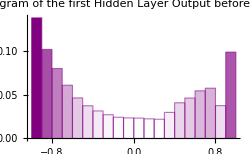
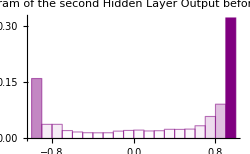
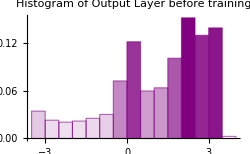

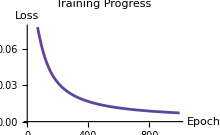

{-Graphics3D-,-Graphics3D-}

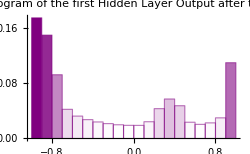
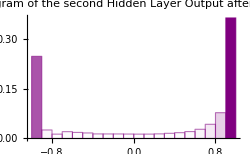
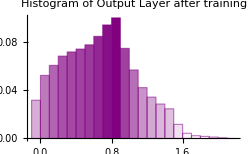

```mathematica
f[x_,y_]:=x^2+y^2;

xValues=Table[x,{x,-1,1,0.01}];
yValues=Table[y,{y,-1,1,0.01}];

trainingData=Flatten[
Table[
{x,y,f[x,y]},
{x,xValues},
{y,yValues}
],1];

m=Length[trainingData];

inputData=Transpose[trainingData[[All,1;;2]]];
outputData={trainingData[[All,3]]};

(*Neural network architecture:*)
numL=3; (*Number of layers.*)
n0=2; (*Number of neurons in input layer.*)
n1=10; (*Number of neurons in hidden layer 1.*)
n2=10; (*Number of neurons in hidden layer 2.*)
n3=1; (*Number of neurons in output layer.*)

SeedRandom[123];
weights1=RandomVariate[NormalDistribution[0,1],{n1,n0}];
biases1=Transpose[{RandomVariate[NormalDistribution[0,1],n1]}];
biasesmatrix1=Transpose[Table[Flatten[biases1],m]];

weights2=RandomVariate[NormalDistribution[0,1],{n2,n1}];
biases2=Transpose[{RandomVariate[NormalDistribution[0,1],n2]}];
biasesmatrix2=Transpose[Table[Flatten[biases2],m]];

weights3=RandomVariate[NormalDistribution[0,1],{n3,n2}];
biases3=Transpose[{RandomVariate[NormalDistribution[0,1],n3]}];
biasesmatrix3=Transpose[Table[Flatten[biases3],m]];

tanhActivation[x_]:=Tanh[x]

tanhDerivative[x_]:=1-Tanh[x]^2

forwardPropagation[inputs_]:=Module[
{preActivlayer1,postActivlayer1,preActivlayer2,postActivlayer2,preActivlayer3,postActivlayer3},

preActivlayer1=(weights1.inputs+biasesmatrix1);
postActivlayer1=Map[tanhActivation,preActivlayer1];

preActivlayer2=(weights2.postActivlayer1+biasesmatrix2);
postActivlayer2=Map[tanhActivation,preActivlayer2];

preActivlayer3=(weights3.postActivlayer2+biasesmatrix3);
postActivlayer3=preActivlayer3;

{preActivlayer1,postActivlayer1,preActivlayer2,postActivlayer2,preActivlayer3,postActivlayer3}
];

{preActivlayer1,layer1Output,preActivlayer2,layer2Output,preActivlayer3,layer3Output}=forwardPropagation[inputData];

NNOutPutData=Transpose[Join[inputData,layer3Output]];

Table[
ListPlot3D[
data[[2]],
PlotLabel->Style[Row[{"3D plot for ",data[[1]]}]],
ColorFunction->"Rainbow",
ImageSize->220
],
{data,{{"training Data \n before training",trainingData},{"NN output data \n before training",NNOutPutData}}}
]

Table[
Histogram[
Flatten[layer[[2]]],
Automatic,
"Probability",
PlotLabel->Style[Row[{"Histogram of ",layer[[1]]}]],
FrameLabel->{"Output","Probability"},
ColorFunction->Function[{height},Opacity[height]],
ChartStyle->Purple,
ImageSize->250
],
{layer,
{
{"the first Hidden Layer \n Output before training",layer1Output},
{"the second Hidden Layer \n Output before training",layer2Output},
{"Output Layer \n before training",layer3Output}
}
}
]

mseLoss[yActual_,yPredicted_]:=Mean[Flatten[(yPredicted-yActual)^2]]

learningRate=0.1;
numEpochs=1000;

Do[
{preActivlayer1,layer1Output,preActivlayer2,layer2Output,preActivlayer3,layer3Output}=forwardPropagation[inputData];

currentLoss=mseLoss[outputData,layer3Output];

delta3=(layer3Output-outputData);
gradWeights3=(1/m)*delta3.Transpose[layer2Output];
gradBiases3=(1/m)*{{Total[Flatten[delta3]]}};

delta2=(Transpose[weights3].delta3)*Map[tanhDerivative,preActivlayer2];
gradWeights2=(1/m)*delta2.Transpose[layer1Output];
gradBiases2=(1/m)*Transpose[{Total[Transpose[delta2]]}];

delta1=(Transpose[weights2].delta2)*Map[tanhDerivative,preActivlayer1];
gradWeights1=(1/m)*delta1.Transpose[inputData];
gradBiases1=(1/m)*Transpose[{Total[Transpose[delta1]]}];

weights3=weights3-learningRate*gradWeights3;
biases3=biases3-learningRate*gradBiases3;
biasesmatrix3=Transpose[Table[Flatten[biases3],m]];

weights2=weights2-learningRate*gradWeights2;
biases2=biases2-learningRate*gradBiases2;
biasesmatrix2=Transpose[Table[Flatten[biases2],m]];

weights1=weights1-learningRate*gradWeights1;
biases1=biases1-learningRate*gradBiases1;
biasesmatrix1=Transpose[Table[Flatten[biases1],m]];

lastEpoch=epoch;
trainingprogress[epoch]={epoch,currentLoss};
If[currenLoss<0.0001,Break[]];,
{epoch,numEpochs}
];

ListPlot[
Table[trainingprogress[i],{i,1,lastEpoch}],
PlotLabel->"Training Progress",
AxesLabel->{"Epoch","Loss"},
Joined->True,
ColorFunction->"Rainbow",
ImageSize->220
]

{preActivlayer1n,layer1Outputn,preActivlayer2n,layer2Outputn,preActivlayer3n,layer3Outputn}=forwardPropagation[inputData];

NNOutPutDatan=Transpose[Join[inputData,layer3Outputn]];

Table[
ListPlot3D[
data[[2]],
PlotLabel->Style[Row[{"3D plot for ",data[[1]]}]],
ColorFunction->"Rainbow",
ImageSize->220
],
{data,{{"training Data \n after training",trainingData},{"output data \n after training",NNOutPutDatan}}}
]

Table[
Histogram[
Flatten[layer[[2]]],
Automatic,
"Probability",
PlotLabel->Style[Row[{"Histogram of ",layer[[1]]}]],
FrameLabel->{"Output","Probability"},
ColorFunction->Function[{height},Opacity[height]],
ChartStyle->Purple,
ImageSize->250
],
{layer,
{
{"the first Hidden Layer \n Output after training",layer1Outputn},
{"the second Hidden Layer \n Output after training",layer2Outputn},
{"Output Layer \n after training",layer3Outputn}
}
}
]
```

code 4.2

(* The code demonstrates training a neural network to approximate a given function and visualizing the learned function’s surface. The code aims to achieve the following: Generate a dataset consisting of input-output pairs where the inputs are coordinates (x,y) and the outputs are the result of the function x^2+y^2. Construct a neural network architecture with two hidden layers, each containing 10 neurons with hyperbolic tangent activation functions, and an output layer with a single neuron. Train the neural network using the generated dataset to learn the relationship between the input coordinates and the corresponding function values. Visualize the learned function by plotting its 3D surface over a specified range of x and y values: *)

```mathematica
data=Flatten@Table[
{x,y}->x^2+y^2,
{x,-1,1,0.01},
{y,-1,1,0.01}
];

neuralNet=NetChain[{10,Tanh,10,Tanh,1}];
trainedNet=NetTrain[neuralNet,data,BatchSize->1024]

Plot3D[
trainedNet[{x,y}],
{x,-2,2},
{y,-2,2},
NormalsFunction->None,
ColorFunction->"Rainbow",
ImageSize->220]
```

Comparing SGD and Full batch Gradient Descent (FBGD) provides insights into their respective strengths and weaknesses. The goal of the Mathematica Code 4.3 and Mathematica Code 4.4 are to implement FBGD and SGD, respectively, for linear regression using basic NN with a single neuron, one input, and one bias term.

Below are the main steps of Mathematica Code 4.3:

1. Define a cost function that measures the squared error between the predicted values and the actual values of the dataset.

2. Define the gradient of the cost function with respect to the model parameters (weights and bias) using the chain rule of differentiation.

3. Implement a FBGD algorithm that updates the model parameters using the gradients computed over the entire dataset at each iteration.

4. Visualize the linear regression model fitted to the dataset after running FBGD. This includes plotting the dataset and the regression line.

5. Plot the magnitude of the gradients over the iterations to observe the convergence behavior of the optimization algorithm.

6. Plot the gradients of the cost function with respect to the model parameters (weights and bias) over the iterations to understand how they change during optimization.

7. Plot the value of the cost function over the iterations to monitor the optimization progress and convergence.

8. Plot the values of the model parameters (weights and bias) over the iterations to observe how they change during optimization.

In comparison to SGD, Mathematica Code 4.4, which updates the model parameters using gradients computed from individual data points randomly sampled from the dataset, FBGD computes gradients using the entire dataset, Mathematica Code 4.3. This fundamental difference in sampling methodology leads to distinct convergence behaviors between the two optimization algorithms.

For example, the figure “Cost Function over 1000 Iterations”, Mathematica Code 4.3, for FBGD typically shows smoother convergence compared to SGD, Mathematica Code 4.4, where the cost function tends to exhibit more fluctuations due to the randomness in selecting individual data points for computing gradients. While SGD can sometimes converge faster due to more frequent parameter updates, FBGD often provides more stable convergence and a smoother decrease in the cost function. However, FBGD may be computationally more expensive since it requires processing the entire dataset at each iteration.

In FBGD, the entire training dataset is used to compute the gradient of the cost function in each iteration. As a result, the cost function surface remains static throughout the training process since the gradient is calculated using all data points at once. Therefore, the plot displays a single static error surface. On the other hand, for SGD, only a single data point is used to compute the gradient in each iteration. This leads to more stochastic updates of the parameters and hence, a dynamic error surface (many error surfaces).

When visualizing various aspects such as magnitude of the gradient, evolution of weights and biases, cost function dynamics, and parameter values over iterations, FBGD consistently exhibits smoother curves compared to SGD. Conversely, SGD’s reliance on stochastic updates often manifests in curves with more pronounced fluctuations and variability.

code 4.3

(* The code implements a basic neural network with a single neuron, one input, and one bias term, primarily aimed at solving a linear regression problem. It utilizes the mean squared error (MSE) as the cost function to quantify the disparity between predicted and actual output values. Employing full batch gradient descent, the model iteratively adjusts its parameters, namely the weight connecting the input to the neuron and the bias, to minimize the cost function. Through visualization techniques such as plotting the gradient magnitude, gradients of the cost function with respect to the model parameters, cost function evolution, and parameter values over iterations, the code offers insights into the training process, enabling an understanding of how the model learns to make predictions based on input data: *)

Final values: w = 2.1105, b = 2.46132

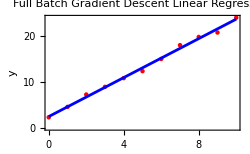

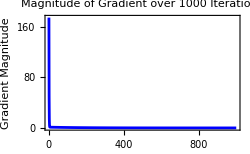

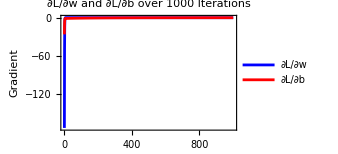

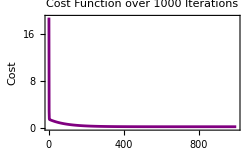

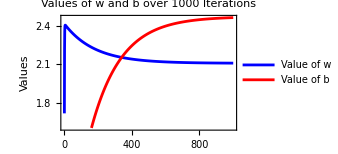

-Graphics3D-

```mathematica
Clear[x,y,w,b];

costFunction[x_,y_,w_,b_]=(y-(w*x+b))^2;

costGradient[x_,y_,w_,b_]=D[costFunction[x,y,w,b],{{w,b}}];

fullBatchGradientDescent[data_,initialGuess_,learningRate_,iterations_]:=Module[
{w=initialGuess[[1]],b=initialGuess[[2]],n=Length[data],gradientList={},costList={},wValues={},bValues={}},
Do[
gradients=(1/Length[data])*Total[costGradient[#[[1]],#[[2]],w,b]&/@data];
gradientList=Append[gradientList,gradients];

w-=learningRate*gradients[[1]];
b-=learningRate*gradients[[2]];
AppendTo[wValues,w];
AppendTo[bValues,b];

costs=(1/Length[data])*Total[costFunction[#[[1]],#[[2]],w,b]&/@data];
costList=Append[costList,costs],
{iterations}
];
{w,b,gradientList,costList,wValues,bValues}
];

data=Table[
{x,2*x+3+RandomReal[{-1,1}]},
{x,0,10}];

initialGuess={0.,0.}; learningRate=0.01; iterations=1000;
{finalW,finalB,gradientList,costList,wValues,bValues}=fullBatchGradientDescent[data,initialGuess,learningRate,iterations];

errors=Flatten[
Table[
{w,b,(1/Length[data])*Total[costFunction[#[[1]],#[[2]],w,b]&/@data]},
{w,0,4,0.1},
{b,0,4,0.1}
],
1];

Print["Final values: w = ",finalW,", b = ",finalB];

Show[
ListPlot[
data,
PlotStyle->Red,
PlotLegends->Placed[{"Data"},{0.55,0.1}],
ImageSize->250
],
Plot[finalW*x+finalB,
{x,0,10},
PlotStyle->Blue,
PlotLegends->Placed[{"Regression Line"},{0.55,0.1}],
ImageSize->250
],
Frame->True,
FrameLabel->{"x","y"},
PlotLabel->"Full Batch Gradient Descent Linear Regression"
]

ListLinePlot[
Norm/@gradientList,
PlotStyle->Blue,
Frame->True,
FrameLabel->{"Iterations","Gradient Magnitude"},
PlotLabel->"Magnitude of Gradient over 1000 Iterations",
PlotRange->All,
ImageSize->250
]

gradientWList=gradientList[[All,1]];
gradientBList=gradientList[[All,2]];

ListLinePlot[
{gradientWList,gradientBList},
PlotStyle->{Blue,Red},
Frame->True,
FrameLabel->{"Iterations","Gradient"},
PlotLegends->Placed[{"∂L/∂w","∂L/∂b"},{0.70,0.4}],PlotLabel->"∂L/∂w and ∂L/∂b over 1000 Iterations",
PlotRange->All,
ImageSize->250
]

ListLinePlot[
costList,
PlotStyle->Purple,
Frame->True,
FrameLabel->{"Iterations","Cost"},
PlotLabel->"Cost Function over 1000 Iterations",
PlotRange->All,
ImageSize->250
]

ListLinePlot[
{wValues,bValues},
PlotStyle->{Blue,Red},
Frame->True,
FrameLabel->{"Iterations","Values"},
PlotLegends->Placed[{"Value of w","Value of b"},{0.75,0.4}],
PlotLabel->"Values of w and b over 1000 Iterations",
ImageSize->250
]

Show[
ListPlot3D[
errors,
PlotLegends->Automatic,
ColorFunction->"Rainbow",
PlotRange->Full,
PlotLabel->"Cost Function Surface and Updates \n of (w,b,cost) Over 1000 Epochs",
AxesLabel->{"w","b","Cost"},
ImageSize->250
],
ListLinePlot3D[
Transpose[{wValues,bValues,costList}],
PlotStyle->Directive[Opacity[0.5],Red],
AxesLabel->{"w","b","Cost"},
PlotRange->Full,
ImageSize->250
]
]
```

code 4.4

(* While both Mathematica codes 4.3 and 4.4 cover similar aspects, such as visualizing the training process and optimization metrics, the differences lie in the optimization algorithm. Mathematica code 4.4 uses SGD: *)

Final values: w = 1.98006, b = 2.70102

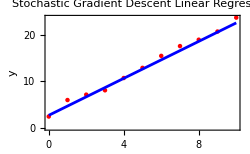

-Graphics3D-

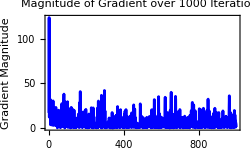

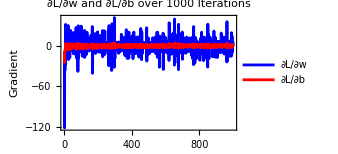

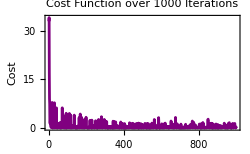

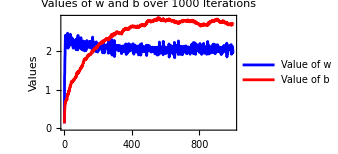

-Graphics3D-

```mathematica
Clear[x,y,w,b];

costFunction[x_,y_,w_,b_]=(y-(w*x+b))^2;

costGradient[x_,y_,w_,b_]=D[costFunction[x,y,w,b],{{w,b}}];

stochasticGradientDescent[data_,initialGuess_,learningRate_,iterations_]:=Module[
{w=initialGuess[[1]],b=initialGuess[[2]],n=Length[data],gradient,x,y,gradientList,costList,wValues,bValues},
gradientList={};
costList={};
wValues={};
bValues={};
Do[
{x,y}=RandomChoice[data];
gradient=costGradient[x,y,w,b];
gradientList=Append[gradientList,gradient];
w-=learningRate*gradient[[1]];
b-=learningRate*gradient[[2]];
AppendTo[wValues,w];
AppendTo[bValues,b];
cost=costFunction[x,y,w,b];
costList=Append[costList,cost],
{iterations}
];
{w,b,gradientList,costList,wValues,bValues}
];

data=Table[
{x,2*x+3+RandomReal[{-1,1}]},
{x,0,10}];
initialGuess={0.,0.};
learningRate=0.01;
iterations=1000;
{finalW,finalB,gradientList,costList,wValues,bValues}=stochasticGradientDescent[data,initialGuess,learningRate,iterations];

Print["Final values: w = ",finalW,", b = ",finalB];

Show[
ListPlot[
data,
PlotStyle->Red,
PlotLegends->Placed[{"Data"},{0.55,0.1}],
ImageSize->250
],
Plot[finalW*x+finalB,
{x,0,10},
PlotStyle->Blue,
PlotLegends->Placed[{"Regression Line"},{0.55,0.1}],
ImageSize->250
],
Frame->True,
FrameLabel->{"x","y"},
PlotLabel->"Stochastic Gradient Descent Linear Regression"
]

errors=
Table[
Flatten[
Table[
{w,b,costFunction[w,b,data[[i]][[1]],data[[i]][[2]]]},
{w,-7,7,0.1},
{b,-7,7,0.1}
],
1],
{i,1,Length[data]}
];

ListPlot3D[
errors,
ImageSize->250,
PlotLabel->"Cost Function Surfaces",
PlotStyle->Directive[Opacity[0.4]],
PlotRange->Full
]

ListLinePlot[
Norm/@gradientList,
PlotStyle->Blue,
Frame->True,
FrameLabel->{"Iterations","Gradient Magnitude"},
PlotLabel->"Magnitude of Gradient over 1000 Iterations",
PlotRange->All,
ImageSize->250
]

gradientWList=gradientList[[All,1]];
gradientBList=gradientList[[All,2]];

ListLinePlot[
{gradientWList,gradientBList},
PlotStyle->{Blue,Red},
Frame->True,
FrameLabel->{"Iterations","Gradient"},
PlotLegends->Placed[{"∂L/∂w","∂L/∂b"},{0.70,0.4}],PlotLabel->"∂L/∂w and ∂L/∂b over 1000 Iterations",
PlotRange->All,
ImageSize->250
]

ListLinePlot[
costList,
PlotStyle->Purple,
Frame->True,
FrameLabel->{"Iterations","Cost"},
PlotLabel->"Cost Function over 1000 Iterations",
PlotRange->All,
ImageSize->250
]

ListLinePlot[
{wValues,bValues},
PlotStyle->{Blue,Red},
Frame->True,
FrameLabel->{"Iterations","Values"},
PlotLegends->Placed[{"Value of w","Value of b"},{0.75,0.4}],
PlotLabel->"Values of w and b over 1000 Iterations",
ImageSize->250
]

ListLinePlot3D[
Transpose[{wValues,bValues,costList}],
PlotStyle->Directive[Opacity[0.5],Red],
AxesLabel->{"w","b","Cost"},
PlotRange->Full,
ImageSize->250
]
```

code 4.5

(* case 1, without biases. Suppose we have a neural network with two layers, and the activation function is the identity function (Φ(x)=x) for both layers. In this example, the network effectively behaves as a single layer with the weight matrix W’, demonstrating the reduction of a multi-layer network with identity activation functions to a single-layer network: *)

```mathematica
W1={{2,1},{1,3}};
W2={{1,2},{3,4}};

x={1,2};
y1=W1.x;
y2=W2.y1;
Wprime=W2.W1;
yFinal=Wprime.x;

{y1,y2,Wprime,yFinal}
```

{{4,7},{18,40},{{4,7},{10,15}},{18,40}}

code 4.6

(* case 2, with biases. Suppose we have a neural network with two layers, and the activation function is the identity function (Φ(x)=x) for both layers. In this example, the network effectively behaves as a single layer with the weight matrix W’, demonstrating the reduction of a multi-layer network with identity activation functions to a single-layer network: *)

```mathematica
W1={{2,1},{1,3}};
W2={{1,2},{3,4}};

b1={1,2};
b2={3,4};

x={1,2};
y1=W1.x+b1;
y2=W2.y1+b2;

Wprime=W2.W1;
yFinal=Wprime.x+(W2.b1+b2);

{y1,y2,Wprime,yFinal}
```

{{5,9},{26,55},{{4,7},{10,15}},{26,55}}

code 4.7

(* The goal of the code is to define and visualize a mathematical function referred to as the “rectangular towers function.” This function is constructed by taking the difference between two sigmoid functions with distinct peaks and shifts. The sigmoid functions are defined with a steep slope and a shift parameter, and their specific parameters are set to create a left sigmoid (sigmoidLeft) and a right sigmoid (sigmoidRight). The rectangularTowers function is then formed by subtracting the right sigmoid from the left sigmoid. The resulting function represents a rectangular towers-like structure. The code includes plotting commands to visually represent the rectangular towers function (rectangularTowers) as well as the individual left (sigmoidLeft) and right (sigmoidRight) sigmoid functions: *)

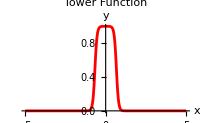

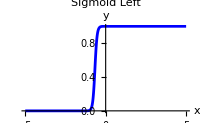

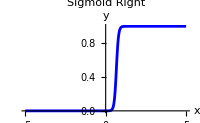

```mathematica
sigmoid[x_,a_,b_]:=1/(1+Exp[a x+b])
sigmoidLeft[x_]:=sigmoid[x,-15,-10]
sigmoidRight[x_]:=sigmoid[x,-15,10]

rectangularTowers[x_]:=sigmoidLeft[x]-sigmoidRight[x]

Plot[
rectangularTowers[x],
{x,-5,5},
PlotRange->All,
AxesLabel->{"x","y"},
PlotLabel->"Tower Function",
ImageSize->200,
PlotStyle->Red
]

Plot[
sigmoidLeft[x],
{x,-5,5},
PlotRange->All,
AxesLabel->{"x","y"},
PlotLabel->"Sigmoid Left",
ImageSize->200,
PlotStyle->Blue
]

Plot[
sigmoidRight[x],
{x,-5,5},
PlotRange->All,
AxesLabel->{"x","y"},
PlotLabel->"Sigmoid Right",
ImageSize->200,
PlotStyle->Blue
]
```

code 4.8

(* The goal of the code is to define and visualize a function f(x) that is the difference between two sigmoid functions. The parameters a and b in the sigmoid function control the shape and position of the curve. The Manipulate function create an interactive plot where you can dynamically adjust the parameters a1, b1, a2, and b2 and observe the corresponding changes in the function f(x): *)

```mathematica
Clear[f,x,a,b,a1,b1,a2,b2];

sigmoid[x_,a_,b_]:=1/(1+Exp[a x+b])

f[x_,a1_,b1_,a2_,b2_]:=sigmoid[x,a1,b1]-sigmoid[x,a2,b2]

a1=2;b1=1;
a2=3;b2=-1;

Manipulate[
Plot[
f[x,a1,b1,a2,b2],
{x,-5,5},
PlotStyle->{Thick,Blue},
AxesLabel->{"x","f(x)"},
PlotRange->{-2,2},
ImageSize->250
],
{{a1,2.7,"a1"},0.1,5,0.1},
{{b1,-5,"b1"},-5,5,0.1},
{{a2,2.7,"a2"},0.1,5,0.1},
{{b2,5,"b2"},-5,5,0.1}
]
```

code 4.9

(* We sum two-dimensional sigmoid functions together and plot the result. The result is a ridged surface. Since our goal is to obtain localized bumps we select another pair of two-dimensional sigmoid functions, add them together to get a ridged surface perpendicular to the first ridged surface, and then add the two perpendicular ridged surfaces together. Take two-dimensional sigmoid function to the result which will depress the local minima and saddles to zero while simultaneously sending the central maximum towards 1: *)

```mathematica
sigmoid2D[x_,y_,a_,b_,c_]:=1/(1+Exp[(a x+b y)-c])

f2D[x_,y_,a1_,b1_,a2_,b2_,c1_,c2_]:=sigmoid2D[x,y,a1,b1,c1]-sigmoid2D[x,y,a2,b2,c2]

plotOptions={
ColorFunction->"DarkRainbow",
PlotRange->All,
MeshFunctions->{#3&},
MeshStyle->{{Thin,Purple}},
AxesLabel->{"x","y",""},
ImageSize->200
};

Plot3D[
sigmoid2D[x,y,5,-5,5],
{x,-5,5},
{y,-5,5},
Evaluate@Append[
plotOptions,
PlotLabel->"3D Plot of first sigmoid2D"
]
]

Plot3D[
f2D[x,y,5,-5,5,-5,5,-5],
{x,-5,5},
{y,-5,5},
Evaluate@Append[
plotOptions,
PlotLabel->"3D Plot of ridge"
]
]

Plot3D[
f2D[x,y,5,-5,5,-5,5,-5]+f2D[x,y,-5,-5,-5,-5,5,-5],
{x,-5,5},
{y,-5,5},
Evaluate@Append[
plotOptions,
PlotLabel->"3D Plot of ridge"
]
]

Plot3D[
Module[
{x1,y1},
x1=f2D[x,y,5,-5,5,-5,5,-5];
y1=f2D[x,y,-5,-5,-5,-5,5,-5];
sigmoid2D[x1,y1,-15,-15,-25]
],
{x,-5,5},
{y,-5,5},
Evaluate@Append[
plotOptions,
PlotLabel->"3D Plot of bump"
]
]
```

-Graphics3D-

-Graphics3D-

-Graphics3D-

«1 more identical outputs»

code 4.10

(* The code aims to create an interactive environment for exploring the behavior of two-dimensional sigmoid functions and their differences, allowing users to visualize the impact of changing parameter values on the resulting plots. We sum two-dimensional sigmoid functions together and plot the result. The result is a ridged surface. Since our goal is to obtain localized bumps we select another pair of two-dimensional sigmoid functions, add them together to get a ridged surface perpendicular to the first ridged surface, and then add the two perpendicular ridged surfaces together. Take two-dimensional sigmoid function to the result which will depress the local minima and saddles to zero while simultaneously sending the central maximum towards 1: *)

```mathematica
sigmoid2D[x_,y_,a_,b_,c_]:=1/(1+Exp[(a x+b y)-c])

f2D[x_,y_,a1_,b1_,a2_,b2_,c1_,c2_]:=sigmoid2D[x,y,a1,b1,c1]-sigmoid2D[x,y,a2,b2,c2]

commonPlotSettings={
ColorFunction->"DarkRainbow",
PlotRange->All,
MeshFunctions->{#3&},
MeshStyle->{{Thin,Purple}},
AxesLabel->{"x","y","f(x,y)"},
ImageSize->250
};

createPlot3D[func_,{x_,xMin_,xMax_},{y_,yMin_,yMax_},plotLabel_]:=Plot3D[
func,
{x,xMin,xMax},
{y,yMin,yMax},
Evaluate@Append[
commonPlotSettings,
PlotLabel->plotLabel
]
]

Manipulate[
Column[
{
{
createPlot3D[
sigmoid2D[x,y,a1,b1,c1],
{x,-5,5},
{y,-5,5},
"3D Plot of first sigmoid2D"
],
createPlot3D[
sigmoid2D[x,y,a2,b2,c2],
{x,-5,5},
{y,-5,5},
"3D Plot of second sigmoid2D"
]
},
{
createPlot3D[
f2D[x,y,a1,b1,a2,b2,c1,c2],
{x,-5,5},
{y,-5,5},
"3D Plot of first f(x,y)"
],
createPlot3D[
f2D[x,y,a3,b3,a4,b4,c3,c4],
{x,-5,5},
{y,-5,5},
"3D Plot of second f(x,y)"
]
},
{
createPlot3D[
f2D[x,y,a1,b1,a2,b2,c1,c2]+f2D[x,y,a3,b3,a4,b4,c3,c4],
{x,-5,5},
{y,-5,5},
"3D Plot of intersecting ridges"
],
createPlot3D[
sigmoid2D[f2D[x,y,a1,b1,a2,b2,c1,c2],f2D[x,y,a3,b3,a4,b4,c3,c4],a,b,c],
{x,-5,5},
{y,-5,5},
"3D Plot of bump"
]
}
}
],
{{a1,5,"a1"},-5,5,0.1},{{b1,-5,"b1"},-5,5,0.1},{{a2,5,"a2"},-5,5,0.1},{{b2,-5,"b2"},-5,5,0.1},{{c1,5,"c1"},-5,5,0.1},{{c2,-5,"c2"},-5,5,0.1},{{a3,-5,"a3"},-5,5,0.1},{{b3,-5,"b3"},-5,5,0.1},{{a4,-5,"a4"},-5,5,0.1},{{b4,-5,"b4"},-5,5,0.1},{{c3,5,"c3"},-5,5,0.1},{{c4,-5,"c4"},-5,5,0.1},{{a,-15,"a"},-15,10,0.1},{{b,-15,"b"},-15,10,0.1},{{c,-25,"c"},-25,10,0.1} ]
```

### Layers: LinearLayer and ElementwiseLayer

#### LinearLayer

A LinearLayer represents a fully connected layer where each neuron in the layer is connected to every neuron in the preceding layer. When you use a LinearLayer, you’re effectively introducing a set of neurons in your NN, each performing a linear transformation on the input data.

LinearLayer[n]		represents a trainable, fully connected net layer that computes 𝑾∙𝒙+𝒃 with output vector of size n.

LinearLayer[{n1,n2,…}]	represents a layer that outputs an array of dimensions n1×n2×….

LinearLayer[]		leaves the dimensions of the output array to be inferred from context.

LinearLayer[n,opts]	includes options for initial weights and other parameters.

• The following optional parameters can be included:

“Biases” 	Automatic 	initial vector of biases (𝒃 in 𝑾.𝒙+𝒃)

“Weights” 	Automatic 	initial matrix of weights (𝑾 in 𝑾.𝒙+𝒃)

• When you create a NN layer in Mathematica using LinearLayer and don’t specify weights and biases explicitly, they are automatically generated when you initialize the network using NetInitialize or train it using NetTrain.

• “Biases”->None: This setting is used to explicitly specify that biases should not be used in the layer.

• When you apply a LinearLayer to input data, LinearLayer[…][input], it computes the output by applying the learned weights and biases (if any) to the input data.

• If you provide a list of inputs {input1, input2, ...} to a LinearLayer, it computes the outputs for each of these inputs separately.

• The NetExtract function in Mathematica can be used to extract specific parts (such as weights and biases) from a trained NN. For a LinearLayer object, you can use NetExtract to retrieve its weights and biases.

• If you specify LinearLayer[{}], it indicates that the LinearLayer should produce a single real number as output. This is useful in scenarios where you want the output of the layer to be a scalar value.

• LinearLayer[n, “Input”->m]: This is indeed a common usage pattern for LinearLayer. It represents a linear layer that takes a vector of length m as input and produces a vector of length n as output. This is a fundamental building block in many NN architectures, where fully connected layers transform input vectors into output vectors.

• In larger NN architectures, sometimes the input shape of a specific layer cannot be inferred from previous layers. In such cases, you can use the “Input”->shape option with LinearLayer to fix the input shape. The shape parameter can take various forms to specify the input shape, allowing you to define the structure of the network more explicitly.

• Note that the layers containing learnable parameters appear in red, indicating that they require initial values before the net can be applied to an input.

“Real” 		a single real number

m 		a vector of length

m {m1,m2,…} 	an array of dimensions m1×m2×…

code 4.11

(* Create a LinearLayer whose output is a length-5 vector: *)

```mathematica
LinearLayer[5]
```

LinearLayer[…]

code 4.12

(* In this example: {{1,2,3}, {4,5,6}} is a custom 2x3 weight matrix. {0.5, -1} is a custom bias vector with length equal to the number of outputs (2 in this case). LinearLayer[2,”Input”->3] creates a linear layer with 3 inputs and 2 outputs. RandomReal[1,{3,3}] generates a random matrix with 3 samples and 3 features as input data. These custom weights and biases are then used to create a LinearLayer with the specified parameters. The customLinearLayer[inputData] applies this custom linear layer to the input data: *)

```mathematica
customWeights={{1,2,3},{4,5,6}};
customBiases={0.5,-1};

customLinearLayer=LinearLayer[2,"Input"->3,"Weights"->customWeights,"Biases"->customBiases]

inputData=RandomReal[1,{3,3}]
outputData=customLinearLayer[inputData]
```

LinearLayer[…]

{{0.282295,0.305087,0.236187},{0.283116,0.715522,0.619318},{0.72189,0.149645,0.273242}}

{{2.10103,3.07174},{4.07211,7.42598},{2.34091,4.27524}}

code 4.13

(* In this example: Biases->None indicates that no biases should be used. The custom weight matrix is specified as {{1,2,3},{4,5,6}}. The resulting customLinearLayer is then applied to the example input data: *)

```mathematica
customWeights={{1,2,3},{4,5,6}};

customLinearLayer=LinearLayer[2,"Input"->3,"Weights"->customWeights,"Biases"->None]

inputData=RandomReal[1,{2,3}]
outputData=customLinearLayer[inputData]

weights=NetExtract[customLinearLayer,"Weights"]
Normal[weights]
```

LinearLayer[…]

{{0.559594,0.900463,0.814698},{0.273156,0.21203,0.0413252}}

{{4.80461,11.6289},{0.821192,2.40072}}

NumericArray[…]

{{1.,2.,3.},{4.,5.,6.}}

code 4.14

(* The code creates a LinearLayer with specified input and output dimensions. It then uses NetInitialize to randomly initialize the layer’s weights and biases. The code generates example input data and applies the initialized linear layer to compute the corresponding output: *)

```mathematica
inputSize=2;
outputSize=3;

uninitializedLinearLayer=LinearLayer[outputSize,"Input"->inputSize]

randomlyInitializedLinearLayer=NetInitialize[uninitializedLinearLayer]

inputData=RandomReal[1,{2,inputSize}]
outputData=randomlyInitializedLinearLayer[inputData]
```

LinearLayer[…]

LinearLayer[…]

{{0.835404,0.617059},{0.0190568,0.414784}}

{{-0.331089,-0.27109,1.00739},{-0.0275572,0.4292,-0.350135}}

code 4.15

(* Define and initialize a LinearLayer without biases: *)

```mathematica
linear=NetInitialize@LinearLayer[3,"Biases"->None,"Input"->2]
```

LinearLayer[…]

code 4.16

(* The code demonstrates the manual computation of a linear transformation and compares it with the result obtained using the built-in LinearLayer. The linear function is defined to perform the transformation, taking input data, a weight matrix, and a bias vector. The code initializes a LinearLayer with specified input and output dimensions, applies it to example data, and then manually computes the transformation using extracted weights and biases. The primary goal is to illustrate the equivalence of results between the manual computation and the LinearLayer, providing insights into the underlying linear transformation process within neural networks: *)

```mathematica
Clear[data,weight,bias,linear];

linear[data_,weight_,bias_]:=Dot[weight,data]+bias

data={2,10,3};

layer=NetInitialize@LinearLayer[2,"Input"->3]
layer[data]

linearResult=linear[
data,
NetExtract[layer,"Weights"]//Normal,
NetExtract[layer,"Biases"]//Normal
]
```

LinearLayer[…]

{-3.75531,14.955}

{-3.75531,14.955}

#### ElementwiseLayer

The ElementwiseLayer is used to introduce element-wise non-linearities or transformations to the output of a NN layer.

ElementwiseLayer[f]		represents a net layer that applies a unary function f to every element of the input array.

ElementwiseLayer[“name”]	applies the function specified by “name”.

• The function f can be any one of the following: Ramp, LogisticSigmoid, Tan, Tanh, ArcTan, ArcTanh, Sin, Sinh, ArcSin, ArcSinh, Cos, Cosh, ArcCos, ArcCosh, Cot, Coth, ArcCot, ArcCoth, Csc, Csch, ArcCsc, ArcCsch, Sec, Sech, ArcSec, ArcSech, Haversine, InverseHaversine, Gudermannian, InverseGudermannian, Log, Exp, Sqrt, CubeRoot, Abs, Gamma, LogGamma, Erf, InverseErf, Erfc, InverseErfc, Round, Floor, Ceiling, Sign, FractionalPart, IntegerPart, Unitize, KroneckerDelta.

• In general, f can be any object that when applied to a single argument gives any combination of Ramp, LogisticSigmoid, etc., together with numbers, Plus, Subtract, Times, Divide, Power, Surd, Min, Max, Clip, Mod, Threshold, Chop and some logical operations using If, And, Or, Which, Piecewise, Equal, Greater, GreaterEqual, Less, LessEqual, Unequal, Negative, NonNegative, Positive, NonPositive, PossibleZeroQ.

• ElementwiseLayer 				supports the following values for “name”:

“RectifiedLinearUnit” or “ReLU” 		Ramp[x]

“ExponentialLinearUnit” or “ELU” 		x when x≥0; Exp[x]-1 when x<0

“ScaledExponentialLinearUnit” or “SELU” 	1.0507 x when x >= 0; 1.758099340847161`(Exp[x]-1) when x<0

“GaussianErrorLinearUnit” or “GELU” 	0.5 x(1+Erf[x/Sqrt[2]])

“Swish” 					x LogisticSigmoid[x]

“HardSwish” 					x Min[Max[x+3,0],6]/6

“Mish” 						x Tanh[Log[1+Exp[x]]]

“SoftSign” 					x/(1+Abs[x])

“SoftPlus” 					Log[Exp[x]+1]

“HardTanh” 					Clip[x,{-1,1}]

“HardSigmoid” 				Clip[(x+1)/2, {0,1}]

“Sigmoid” 					LogisticSigmoid[x]

• When you apply an ElementwiseLayer to a single input ElementwiseLayer[..][input], it explicitly computes the output by applying the layer’s operation to the input. This operation could be any element-wise function or operation specified when creating the ElementwiseLayer.

• If you provide a list of inputs {input1, input2, ...} to an ElementwiseLayer, ElementwiseLayer[..][{input1, input2, ...}], it explicitly computes the outputs for each of these inputs separately. Each input will undergo the same element-wise operation independently.

• In a larger NN architecture, sometimes it’s necessary to explicitly specify the dimensions of the input to an ElementwiseLayer. This is particularly important when the input dimensions cannot be inferred from previous layers. In such cases, you can use the “Input”->{n1, n2, ...} option to fix the input dimensions of the ElementwiseLayer.

code 4.17

(* This Mathematica code demonstrates the creation of an ElementwiseLayer using the Tanh function and showcases its application to a single vector. Additionally, it provides a plot to visualize the Tanh function’s behavior over a specified input range: *)

ElementwiseLayer[…]

{-0.995055,-0.964028,-0.761594,0.,0.761594,0.964028,0.995055}

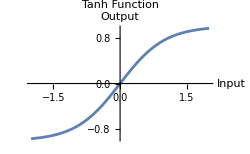

```mathematica
tanh=ElementwiseLayer[Tanh]

tanh[{-3,-2,-1,0,1,2,3}]
range=Range[-2,2,0.1];
resultVector=tanh/@range;

ListLinePlot[
Transpose[{range,resultVector}],
AxesLabel->{"Input","Output"},
PlotLabel->"Tanh Function",
ImageSize->250
]
```

code 4.18

ElementwiseLayer[…]

{-1.,-1.,-1.,0.,1.,1.,1.}

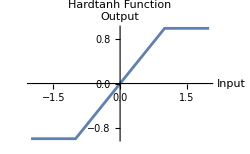

```mathematica
hardtanh=ElementwiseLayer["HardTanh"]

hardtanh[{-3,-2,-1,0,1,2,3}]

range=Range[-2,2,0.1];
resultVector=hardtanh/@range;

ListLinePlot[
Transpose[{range,resultVector}],
AxesLabel->{"Input","Output"},
PlotLabel->"Hardtanh Function",
ImageSize->250
]
```

code 4.19

ElementwiseLayer[…]

{0.,0.,0.,0.,1.,2.,3.}

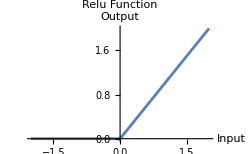

```mathematica
ramp=ElementwiseLayer[Ramp]

ramp[{-3,-2,-1,0,1,2,3}]

range=Range[-2,2,0.1];
resultVector=ramp/@range;

ListLinePlot[
Transpose[{range,resultVector}],
AxesLabel->{"Input","Output"},
PlotLabel->"Relu Function",
ImageSize->250
]
```

code 4.20

(* This code illustrates the creation of an ElementwiseLayer designed for vectors of size 3, and it demonstrates how the layer operates on both a single vector and a batch of vectors, applying the specified activation function (Ramp): *)

```mathematica
elem=ElementwiseLayer[Ramp,"Input"->3]
elem[{1,2,3}]
elem[{{1,2,3},{-1,-2,-3}}]
```

ElementwiseLayer[…]

{1.,2.,3.}

{{1.,2.,3.},{0.,0.,0.}}

code 4.21

(* The code demonstrates the application of the ElementwiseLayer to specific vector and a range of values, and it visualizes the input-output relationship using a ListPlot: *)

{4.71828,11.3891,26.0855}

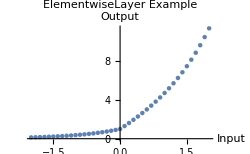

```mathematica
elem=ElementwiseLayer[2*Ramp[#]+Exp[#]&];
resultVector=elem[{1,2,3}]
range=Range[-2,2,0.1];
data=Table[
{range[[i]],elem[range[[i]]]},
{i,1,Length[range]}
];

ListPlot[
data,
ImageSize->250,
PlotRange->All,
AxesLabel->{"Input","Output"},
PlotLabel->"ElementwiseLayer Example"
]
```

code 4.22

(* In this example, the custom function includes operations like Ramp, subtraction, and logarithmic function. The ElementwiseLayer is then created using this custom function and applied to a specific input vector and the results are visualized using ListLinePlot: *)

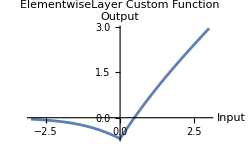

```mathematica
customFunction[x_]:=2*Ramp[x]-Log[1+Exp[x]]

customElementwiseLayer=ElementwiseLayer[customFunction];

range=Range[-3,3,0.1];
resultVector=customElementwiseLayer/@range;

ListLinePlot[
Transpose[{range,resultVector}],
AxesLabel->{"Input","Output"},
PlotLabel->"ElementwiseLayer Custom Function",
ImageSize->250
]
```

code 4.23

(* This example demonstrates how you can use ElementwiseLayer with a combination of elementary mathematical functions (Ramp and Tanh) and a logical operation (If statement) to create a custom elementwise transformation for a given input array. The results are visualized using ListLinePlot: *)

Input Array:
(-2
-1
0
1
2)
Result Array:
(-0.964028
-0.761594
0.
1.
2.)

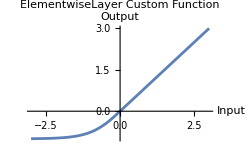

```mathematica
inputArray={-2,-1,0,1,2};
elementwiseLayer=ElementwiseLayer[If[#>0,Ramp[#],Tanh[#]]&];

resultArray=elementwiseLayer[inputArray];

Column[
{
"Input Array:",MatrixForm[inputArray],
"Result Array:",MatrixForm[resultArray]
}
]

range=Range[-3,3,0.1];
resultVector=elementwiseLayer/@range;

ListLinePlot[
Transpose[{range,resultVector}],
AxesLabel->{"Input","Output"},
PlotLabel->"ElementwiseLayer Custom Function",
ImageSize->250
]
```

code 4.24

(* The code defines a custom linear layer in a neural network with specified weights and biases, then applies it to randomly generated input data. Subsequently, an elementwise activation layer with the Rectified Linear Unit (ReLU) activation function is created and applied to the output of the custom linear layer. This process effectively demonstrates the construction of a custom layer in a neural network architecture, showcasing how to set custom parameters and apply activation functions to manipulate the output of the network: *)

```mathematica
customWeights={{1,2,3},{4,5,6},{4,3,2}};
customBiases={0.5,-1,0.1};

customLinearLayer=LinearLayer[3,"Input"->3,"Weights"->customWeights,"Biases"->customBiases]

inputData=RandomReal[1,{3,3}]
preactivation=customLinearLayer[inputData]
activation=ElementwiseLayer[Ramp,"Input"->3]
activation[preactivation]
```

LinearLayer[…]

{{0.291999,0.165718,0.45762},{0.484322,0.163162,0.493848},{0.218203,0.796845,0.48261}}

{{2.4963,3.74231,2.68039},{2.79219,4.71619,3.51447},{3.75972,6.7527,4.32857}}

ElementwiseLayer[…]

{{2.4963,3.74231,2.68039},{2.79219,4.71619,3.51447},{3.75972,6.7527,4.32857}}

code 4.25

(* The code aims to demonstrate the initialization and application of a custom linear layer within a neural network architecture. Initially, a linear layer is created with custom weights and biases, followed by the generation of random input data to which the layer is applied, resulting in pre-activation values. An element- wise activation function, specifically the hyperbolic tangent function (Tanh), is then applied to these pre-activation values to obtain post-activation values. Additionally, histograms are generated to visually represent the distributions of the initialized weights, pre-activation data, and post-activation data. This code not only illustrates the process of initializing and utilizing custom layers but also provides insights into the distributions of values at different stages of the neural network’s computation, aiding in understanding its behavior and performance: *)

LinearLayer[…]

ElementwiseLayer[…]

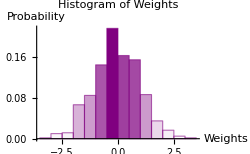
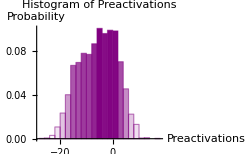
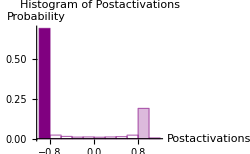

```mathematica
inputSize=200;
outputSize=3;

customWeights=RandomVariate[
NormalDistribution[0,1],
{outputSize,inputSize}
];

customBiases=RandomReal[0,outputSize];

randomlyInitializedLinearLayer=LinearLayer[
outputSize,
"Input"->inputSize,
"Weights"->customWeights,
"Biases"->customBiases
]

inputData=RandomReal[1,{1000,inputSize}];

preactivation=randomlyInitializedLinearLayer[inputData];
preActivationData=Flatten[preactivation];

activationFunction=ElementwiseLayer[Tanh,"Input"->outputSize]
postactivation=activationFunction[preactivation];
postActivationData=Flatten[postactivation];

extractWeights=NetExtract[randomlyInitializedLinearLayer,"Weights"];
extractWeightsData=Flatten[extractWeights];

Table[
Histogram[
index[[2]],
Automatic,
"Probability",
PlotLabel->Style[Row[{"Histogram of ",index[[1]]}]],
AxesLabel->{index[[1]],"Probability"},
ColorFunction->Function[{height},Opacity[height]],
ChartStyle->Purple,
ImageSize->250
],
{index,
{
{"Weights",extractWeightsData},
{"Preactivations",preActivationData},
{"Postactivations",postActivationData}
}
}
]
```

### Containers: NetChain and NetGraph

In Mathematica, NNs are typically built by combining multiple layers together to form a network architecture. While a single NN layer can perform basic transformations on its input data, it’s usually not sufficient for more complex tasks. By combining multiple layers together, you can create deeper and more powerful NNs capable of learning intricate patterns and making more accurate predictions.

• The NetChain container is commonly used to chain layers together sequentially, where the output of one layer serves as the input to the next layer. This sequential structure is suitable for many standard NN architectures.

• However, there are cases where you may need more complex connectivity patterns between layers. For example, you may want to create skip connections, recurrent connections, or other non-sequential connections within the network. In such cases, the NetGraph container is more appropriate. NetGraph allows you to define a graph-like structure where nodes represent different layers or operations, and edges represent the flow of data between them. This flexibility enables you to construct a wide variety of NN architectures tailored to your specific needs.

#### NetChain

NetChain[{layer1,layer2,…}]	specifies a neural net in which the output of layer i is connected to the input of layer i+1.

NetChain[<|”name1”->layer1,”name2”->layer2,…|>]	specifies a net consisting of a chain of explicitly named layers.

• The input data is provided to the NetChain, and it is passed into the first layer specified in the chain. The input data then undergoes sequential processing through each layer in the chain, with the output of one layer serving as the input for the next layer. The final output of the NetChain is taken from the output of the last layer in the chain, providing the result of the network’s computation.

• If the first layer has multiple input ports or the last layer has multiple output ports, the NetChain will have the same input or output ports respectively, allowing for more complex network architectures.

• NetChain[…][data] gives the result of applying the net to data.

• Normal[NetChain[…]] returns a list or association of the layers used to construct the chain.

• NetChain[…][[spec]] extracts the layer specified by spec from the net. This enables users to access and manipulate individual layers within the network.

• The StandardForm of NetChain provides a summary of the layers in the chain, along with the array dimensions of the output of each layer. Clicking on a layer in the chain reveals more detailed information about that specific layer, aiding in network inspection and debugging.

• Note that the layers containing learnable parameters appear in red, indicating that they require initial values before the net can be applied to an input.

• The overall input and output array shapes for the chain can be explicitly specified using the “Input”->shape and “Output”->shape options for NetChain, providing more control over the network’s input and output dimensions.

Possible forms for shape include:

“Real” 				a single real number

“Integer” 			a single integer

Restricted[“Integer”,n] 	an integer between 1 and n

n 				a vector of length n

{n1,n2,…} 			an array of dimensions n1×n2×…

“Varying” 			a vector whose length is variable.

{“Varying”,n2,n3,…} 		an array whose first dimension is variable and remaining dimensions are n2×n3×…

• Any lengths ni given as Automatic are inferred from the structure of the chain, simplifying network construction by automatically determining certain dimensions based on the network’s architecture.

• NetChain[…][data,...,opts] specifies that options should be used when applying the network to data, allowing for additional customization during network evaluation. Possible options include: BatchSize, NetEvaluationMode, RandomSeeding, TargetDevice and WorkingPrecision.

• EdgeList[NetChain[…]] returns the list of connections in the network, providing insights into the network’s connectivity and structure.

• net[data,NetPort[oport]] can be used to obtain the value of the net at oport when it is applied to the specified data. oport must refer to an output port, a subnet of the net, or a layer.

code 4.26

(* The code creates a neural network with three layers, where the first and third layers are linear transformations and the second layer applies a Tanh activation function. The input size is specified as 4, providing a complete description of the network architecture: *)

```mathematica
net=NetChain[
{
LinearLayer[3],
ElementwiseLayer[Tanh],
LinearLayer[1]
},
"Input"->4
]
```

NetChain[…]

code 4.27

(* The code constructs a neural network with explicitly named layers, demonstrates how to extract a specific layer by name using NetExtract, and shows another method using Part syntax for extracting a layer. Explicitly naming layers in a neural network is a good practice, as it enhances code readability and makes it easier to reference and manipulate specific layers later in the code or during analysis. The use of an association (<|...|>) in the NetChain construction is a nice touch. It allows you to associate each layer with a meaningful name, making it clear which layer is being referred to in subsequent operations: *)

```mathematica
net=NetChain[<|
"linear1"->LinearLayer[3],
"activation1"->ElementwiseLayer[Tanh],
"linear2"->LinearLayer[1]
|>]

secondLayer=NetExtract[net,"activation1"]
firstLayer=net[["linear1"]]
```

NetChain[…]

ElementwiseLayer[…]

LinearLayer[…]

code 4.28

(* The code uses a concise syntax to construct a neural network. The network consists of layers specified in a list. Each element in the list represents a layer or a transformation applied to the data. The numeric value “3” indicates the number of nodes in the first layer. The “Tanh” symbol represents the ElementwiseLayer with the hyperbolic tangent (Tanh) activation function applied to its output. The numeric value “4” indicates the number of nodes in the second layer. The “Ramp” symbol represents the activation function applied by the ElementwiseLayer in the second position. The numeric value “5” indicates the number of nodes in the final layer: *)

```mathematica
NetChain[{3,Tanh,4,Ramp,5}]
```

NetChain[…]

code 4.29

(* The code constructs a neural network using the NetChain function with a list of layers. In this case, the network has a structure of 1 node, followed by Ramp activation, 2 nodes, and Tanh activation. The code showcases how to extract the layers of a neural network using the Normal function: *)

```mathematica
net=NetChain[{1,Ramp,2,Tanh}]
Normal[net]
```

NetChain[…]

{LinearLayer[…],ElementwiseLayer[…],LinearLayer[…],ElementwiseLayer[…]}

code 4.30

(* The code defines a neural network in Wolfram Mathematica, net, comprising three element-wise layers: hyperbolic tangent (Tanh), cosine (Cos), and sine (Sin). Through various evaluations, it showcases the extraction of specific layer outputs, including the first layer (Tanh), the first two layers, and all layers, when given input data: *)

```mathematica
net=NetChain[
{
ElementwiseLayer[Tanh],
ElementwiseLayer[Cos],
ElementwiseLayer[Sin]
}
]

net[{-1.2,3.1},NetPort[1,"Output"]]
Tanh[{-1.2,3.1}]

net[{-1.2,3.1},{NetPort[1,"Output"],NetPort[2,"Output"]}]
net[{-1.2,3.1},NetPort[All,"Output"]]

Values[net[{-1.2,3.1},NetPort[All,"Output"]]]
```

NetChain[…]

{-0.833655,0.995949}

{-0.833655,0.995949}

<|NetPort[{1,Output}]→{-0.833655,0.995949},NetPort[{2,Output}]→{0.672174,0.543706}|>

<|NetPort[{1,Output}]→{-0.833655,0.995949},NetPort[{2,Output}]→{0.672174,0.543706},NetPort[{3,Output}]→{0.622689,0.517311}|>

{{-0.833655,0.995949},{0.672174,0.543706},{0.622689,0.517311}}

code 4.31

(* The code constructs, initializes, and analyzes a neural network comprising three layers: a linear layer with 3 output nodes, a Tanh activation layer, and another linear layer with 1 output node. The network is initialized with random weights using the NetInitialize function, making it ready for training or evaluation. A graphical summary of the network’s architecture is displayed using Information[net,”SummaryGraphic”]. Through visualization techniques, such as histograms, the code aims to offer insights into the network’s architecture and behavior. It extracts individual layers for in-depth analysis and examines the distribution of data output from each layer, both sequentially and utilizing NetPort, providing a comprehensive understanding of the network’s functioning and the effects of its activation functions. A 3D plot is generated to visualize the results of the initialized network on a range of input values: *)

NetChain[…]

NetChain[…]

-Graphics-

LinearLayer[…]

ElementwiseLayer[…]

LinearLayer[…]

{{-0.359447,-0.0499231},{-1.12706,1.08654},{1.89365,-0.93114}}

{{-0.631947,0.082531,0.06014}}

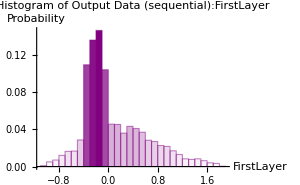
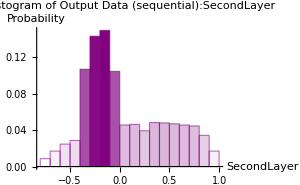
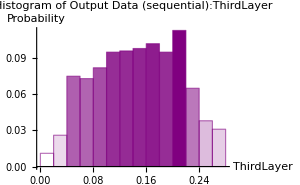

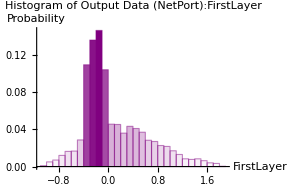
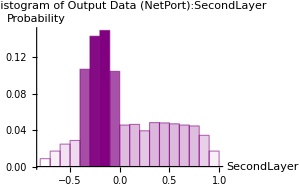
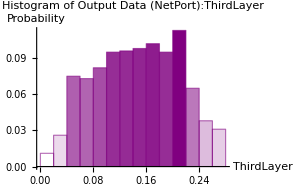

-Graphics3D-

```mathematica
inputDimension=2;

neuralNetwork=NetChain[
{
LinearLayer[3,"Biases"->None],
ElementwiseLayer[Tanh],
LinearLayer[1,"Biases"->None]
},
"Input"->inputDimension
]

neuralNetwork=NetInitialize[neuralNetwork]
Information[neuralNetwork,"SummaryGraphic"]

firstLayer=NetExtract[neuralNetwork,1]
secondLayer=NetExtract[neuralNetwork,2]
thirdLayer=NetExtract[neuralNetwork,3]

NetExtract[neuralNetwork,{1,"Weights"}]//Normal
NetExtract[neuralNetwork,{3,"Weights"}]//Normal

inputData=RandomReal[1,{1000,inputDimension}];

outputFirstLayer=firstLayer[inputData];
outputSecondLayer=secondLayer[outputFirstLayer];
outputThirdLayer=thirdLayer[outputSecondLayer];

Table[
Histogram[
Flatten[layer[[2]]],
Automatic,
"Probability",
PlotLabel->Style[Row[{"Histogram of Output Data (sequential):",layer[[1]]}]],
AxesLabel->{layer[[1]],"Probability"},
ColorFunction->Function[{height},Opacity[height]],
ChartStyle->Purple,
ImageSize->300
],
{layer,{
{"FirstLayer",outputFirstLayer},
{"SecondLayer",outputSecondLayer},
{"ThirdLayer",outputThirdLayer}
}
}
]

outputOfAllLayers=Values[
Table[
neuralNetwork[inputData[[i]],NetPort[All,"Output"]],
{i,1,1000}
]
];

outputFirstLayerNetPort=outputOfAllLayers[[All,1]];
outputSecondLayerNetPort=outputOfAllLayers[[All,2]];
outputThirdLayerNetPort=outputOfAllLayers[[All,3]];

Table[
Histogram[
Flatten[layer[[2]]],
Automatic,
"Probability",
PlotLabel->Style[Row[{"Histogram of Output Data (NetPort):",layer[[1]]}]],
AxesLabel->{layer[[1]],"Probability"},
ColorFunction->Function[{height},Opacity[height]],
ChartStyle->Purple,
ImageSize->300
],
{layer,{
{"FirstLayer",outputFirstLayerNetPort},
{"SecondLayer",outputSecondLayerNetPort},
{"ThirdLayer",outputThirdLayerNetPort}
}
}
]

xValues=Table[x,{x,-2,2,0.1}];
yValues=Table[y,{y,-2,2,0.1}];

trainingData=Flatten[
Table[
{x,y,neuralNetwork[{x,y}][[1]]},
{x,xValues},
{y,yValues}
],1];

ListPlot3D[
trainingData,
PlotLabel->"3D plot for the Initialize Net",
ColorFunction->"Rainbow",
ImageSize->250
]
```

#### NetGraph

NetGraph[{layer1,layer2,…},{m1->n1,m2->n2,…}] specifies a neural net defined by a graph in which the output of layer mi is given as input to layer ni.

NetGraph[<|”name1”->layer1,”name2”->layer2,… ->,{“namem1”->”namen1”,…}] specifies a net with explicitly named layers.

NetGraph[layer] converts a layer or a NetChain into an equivalent minimal NetGraph.

• In Mathematica, NetGraph is a powerful function used for building and representing complex NN architectures as directed acyclic graphs (DAGs). It allows for combining various NN layers and operations

• When constructing a NetGraph in Mathematica, you can create input or output ports for the entire graph by specifying NetPort[“input”]-> or ->NetPort[“output”] respectively in the list of connections.

• In Mathematica’s NetGraph, you can specify a linear chain of connections within the graph using the syntax layer1 -> layer2 -> ... -> layerN. This notation establishes a sequential connection between each layer, where layer1 is connected to layer2, layer2 is connected to layer3, and so on, until layerN. This linear chain notation is useful for defining simple feedforward architectures or for building blocks of more complex networks, such as CNNs or RNNs.

• If the nth layer, or a layer named “layer”, has more than one input or output port, you can disambiguate them by using the syntax NetPort[n, “port”] or NetPort[“layer”, “port”]. By using NetPort with the appropriate layer index or name, you can explicitly specify which input or output port of a layer you want to connect in the NetGraph, allowing for greater control and flexibility in designing complex NN architectures.

• If you leave one or more input or output ports of any layers unconnected within a NetGraph, they will automatically become ports of the entire NetGraph. This behavior allows for more flexibility in connecting multiple NetGraph instances or integrating them into larger network architectures. This behavior facilitates the construction of more modular and reusable network architectures in Mathematica, allowing you to easily combine different components or subnetworks into larger and more complex models.

• In Mathematica’s NetGraph, you can mute some output ports of layers by setting them to None. This is particularly useful when you want to disable certain outputs of a layer within the graph.

• If the NN (NetGraph) has a single input port, you can directly apply the network to input data using the syntax NetGraph[...][data]. This applies the network to the input data and produces the output.

• If the network has multiple input ports, you provide data to each port using an association syntax like NetGraph[...] [<|port1 -> data1, ... |>]. This allows you to specify input data for each input port individually.

• If the network has a single output port, you can still use the syntax NetGraph[...][data] to obtain the output. The output will be the result for that single output port.

• For a net with multiple output ports, NetGraph[…][data] gives an association of the outputs for all ports.

• The StandardForm of NetGraph shows the connectivity of layers in the graph and annotates edges with the dimensions of the array that the edge represents. Clicking a layer or a port in the graph shows more information about that layer or port.

• Normal[NetGraph[…]] returns a list or association of the layers used to construct the graph. EdgeList[NetGraph[…]] returns the list of connections in the graph.

• NetGraph[…][[spec]] extracts the layer specified by spec from the net.

#### NetPort

NetPort[“port”]		represents the specified input or output port for a complete net.

NetPort[{n,”port”}]	represents the specified port for layer number n in a NetGraph or similar construct.

NetPort[{“name”,”port”}]represents the specified port for the layer with the specified name.

code 4.32

(* The code demonstrates a straightforward way to convert a NetChain into a NetGraph in Mathematica, providing flexibility in working with different neural network structures: *)

```mathematica
chain=NetChain[{2,Tanh,3,Ramp}]
NetGraph[chain]
```

NetChain[…]

NetGraph[…]

code 4.33

(* The code defines a simple neural network with a linear chain structure, consisting of two linear layers and one ReLU activation layer. The connections between the layers are specified in a sequential manner: *)

```mathematica
NetGraph[
{
LinearLayer[2],
ElementwiseLayer[Ramp],
LinearLayer[4]
},
{1->2,2->3}
]
```

NetGraph[…]

code 4.34

(* By omitting explicit layer names and using consecutive edge rules, this code provides a concise representation of a neural network with a linear chain structure. The size of the linear layers is specified directly in the layer list. This style can be convenient for simple network structures where explicit names are not necessary: *)

```mathematica
NetGraph[{2,Ramp,4,Ramp,1},{1->2->3->4->5}]
```

NetGraph[…]

code 4.35

(* The code showcases how to construct a NetGraph with explicitly named layers, providing a more human-readable and expressive way to define neural network architectures in Mathematica. The layer names can be used for better documentation and referencing within the code: *)

```mathematica
NetGraph[<|
"linear1"->2,
"ramp1"->Ramp,
"linear2"->2,
"ramp2"->Ramp
|>,
{"linear1"->"ramp1"->"linear2"->"ramp2"}
]
```

NetGraph[…]

code 4.36

(* The code shows that a NetChain object, representing a sequence of layers,can be used as a single layer within a larger NetGraph structure. This allows for flexible and modular construction of neural network architectures: *)

```mathematica
chain=NetChain[{Ramp,LogisticSigmoid}];

NetGraph[{chain,LinearLayer[3]},{1->2}]
```

NetGraph[…]

code 4.37

(* The code showcases the combination of NetGraph and NetChain structures, demonstrating the versatility and composability of these constructs in defining neural network architectures in Mathematica. NetGraph objects with one input and one output can be used as layers inside NetChain objects: *)

```mathematica
net=NetGraph[{1,Ramp,1,LogisticSigmoid},{1->2->3->4}]

net2=NetChain[{1,ElementwiseLayer[Ramp],net}]

NetGraph[net2]
```

NetGraph[…]

NetChain[…]

NetGraph[…]

code 4.38

(* In this example, the NetGraph function is used to create a neural network. It takes two arguments:the list of layers {1,Ramp,2,Tanh} and the connections between layers {1->2->3->4}: *)

```mathematica
net=NetGraph[{1,Ramp,2,Tanh},{1->2->3->4}]

Normal[net]
```

NetGraph[…]

{LinearLayer[…],ElementwiseLayer[…],LinearLayer[…],ElementwiseLayer[…]}

code 4.39

(* In this example, each LinearLayer is followed by a different activation function. The activation functions include ReLU, hyperbolic tangent (Tanh), logistic sigmoid, exponential, sine, and cosine: *)

```mathematica
net=NetGraph[
{
LinearLayer[20],Ramp,

LinearLayer[15],Tanh,

LinearLayer[10],LogisticSigmoid,

LinearLayer[3],Exp,
LinearLayer[2],Sin,
LinearLayer[1],Cos
},
{1->2->3->4->5->6->7->8->9->10->11->12}]
```

NetGraph[…]

code 4.40

(*Construct a net graph with an operation requiring three inputs:*) (* The code constructs a neural network graph using Mathematica’s NetGraph function. It consists of five layers, where the first and third layers each have three neurons and the second and fourth layers apply the Ramp activation function. The fifth layer performs addition. Input data is supplied through a port named “Input”. Connections between layers are established such that the output of the first layer is connected to the input of the second layer, the output of the third layer is connected to the input of the fourth layer, and the input port “Input”, along with the outputs of the second and fourth layers, is connected to the fifth layer. This architecture enables the network to perform an operation requiring three inputs and produce an output based on their combination: *)

```mathematica
NetGraph[
{3,Ramp,3,Ramp,Plus},
{
1->2,
3->4,
{NetPort["Input"],2,4}->5
}
]
```

NetGraph[…]

code 4.41

(* Construct a net graph with multiple inputs: *) (* The NetGraph constructs a neural network with multiple input ports, featuring five layers. The first and third layers consist of three neurons each, while the second and fourth layers apply the Ramp activation function. The fifth layer performs addition. Input data is supplied through three different input ports labeled “Input1”,”Input2”, and “Input3”. Connections between layers are established such that “Input1” is connected to the first layer, “Input2” to the third layer, and “Input3” is jointly connected with the output of the second and fourth layers to the fifth layer. This architecture enables the network to process multiple inputs simultaneously, incorporating them into the network’s operations before producing an output: *)

```mathematica
NetGraph[
{3,Ramp,3,Ramp,Plus},
{
NetPort["Input1"]->1->2,
NetPort["Input2"]->3->4,
{NetPort["Input3"],2,4}->5
}
]
```

NetGraph[…]

code 4.42

(* Construct a net graph with multiple outputs: *) (* The NetGraph constructs a neural network with multiple output ports, consisting of three layers. The first layer comprises 2 neurons, the second layer applies the Ramp activation function, and the third layer performs addition. Input data is supplied through a port named “Input”, and connections between layers are established such that the output of the first layer is connected to the input of the second layer. Furthermore, input data, along with the output of the second layer, is routed to the third layer, where the resulting output is connected to a port named “Output2”. Additionally, the output of the first layer is directly connected to another port named “Output1”. This architecture enables the network to produce multiple outputs simultaneously, offering greater flexibility in network output handling: *)

```mathematica
NetGraph[
{2,Ramp,Plus},
{
1->2,
{NetPort["Input"],2}->3->NetPort["Output2"],
1->NetPort["Output"]
}
]
```

NetGraph[…]

### NetInitialize

NetInitialize[net]       gives a net in which all uninitialized learnable parameters in net have been given initial values.

NetInitialize[net,All] gives a net in which all learnable parameters have been given initial values.

• In Mathematica, the NetInitialize function initializes the parameters of a NN (net) before it’s used for computation. When NetInitialize[net, All] is used, it initializes all parameters, including those that are learnable or trainable.

• However, it’s essential to note that when you initialize the network using NetInitialize[net, All], any existing training or preset learnable parameters in net will indeed be overwritten by the newly initialized parameters. This means that if the network had been previously trained or had preset learnable parameters defined, they will be discarded and replaced with newly initialized parameters.

• In NN initialization, especially when using NetInitialize in Mathematica, weights are typically initialized with random values, and biases are usually initialized to zero.

• This approach is commonly used because it helps introduce some level of randomness into the network’s initial weights, which can aid in breaking symmetry and preventing the network from getting stuck in local minima during training. Random initialization also helps in exploring the solution space more effectively.

• On the other hand, biases are often initialized to zero because they represent the additive constants in the linear transformation of the network’s inputs. Initializing biases to zero ensures that the network starts with a neutral bias before it learns the optimal bias values during training.

• However, it’s worth noting that there are variations and alternatives to these initialization strategies, and different initialization schemes may be more appropriate for different types of networks or tasks. For example, in certain cases, weights may be initialized using specific distributions or scaling techniques to better suit the network architecture or the nature of the data being processed.

The following optional parameters can be included:

Method			“Kaiming”	which initialization method to use

RandomSeeding	1234		seeding of pseudorandom number generator

Possible settings for Method include:

“Kaiming”	choose weights to preserve variance of arrays when propagated through layers, with the method introduced by Kaiming He et al. (2015)

“Xavier”	choose weights to preserve variance of arrays when propagated through layers, with the method introduced by Xavier Glorot et al. (2014)

“Orthogonal”	choose weights to be orthogonal matrices

“Random”	choose weights from a given univariate distribution

“Identity”	choose weights so as to preserve components of arrays when propagated through affine layers

For the method “Random”, the following suboptions are supported:

“Weights”  NormalDistribution[0,1]	random distribution to use to initialize weight matrices

“Biases”     None			random distribution to use to initialize bias vectors

For the methods “Kaiming” and “Xavier”, the following suboption is supported:

“Distribution” 	“Normal”	either “Normal” or “Uniform”

code 4.43

(* The code initializes a neural network with a linear layer of 200 neurons and 2 input dimensions using the “Random” initialization method. “Random” initialization is used, employing normal distributions with a standard deviation of 2 for both weights and biases. The code then extracts and visualizes the initialized weights and biases through histograms: *)

LinearLayer[…]

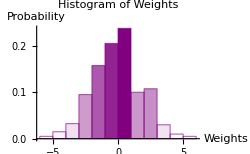

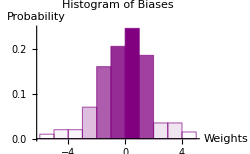

```mathematica
net=NetInitialize[
LinearLayer[200,"Input"->2],
Method->{"Random","Weights"->2,"Biases"->2}
]

Histogram[
Flatten@NetExtract[net,"Weights"],
Automatic,
"Probability",
PlotLabel->"Histogram of Weights",
AxesLabel->{"Weights","Probability"},
ColorFunction->Function[{height},Opacity[height]],
ChartStyle->Purple,
ImageSize->250
]

Histogram[
Flatten@NetExtract[net,"Biases"],
Automatic,
"Probability",
PlotLabel->"Histogram of Biases",
AxesLabel->{"Weights","Probability"},
ColorFunction->Function[{height},Opacity[height]],
ChartStyle->Purple,
ImageSize->250
]
```

code 4.44

(* The code illustrates how setting the random seed to Automatic in the NetInitialize function ensures diverse initializations for repeated calls, while the default behavior results in consistent initialization due to the fixed random seed. This is important for exploring different network initializations during experimentation and training: *)

```mathematica
Normal@NetExtract[NetInitialize[LinearLayer[1,"Input"->1]],"Weights"]
Normal@NetExtract[NetInitialize[LinearLayer[1,"Input"->1]],"Weights"]

Normal@NetExtract[NetInitialize[LinearLayer[1,"Input"->1],RandomSeeding->Automatic],"Weights"]
Normal@NetExtract[NetInitialize[LinearLayer[1,"Input"->1],RandomSeeding->Automatic],"Weights"]
```

{{-0.508336}}

{{-0.508336}}

{{0.636712}}

{{0.863229}}

code 4.45

(* The code creates a base neural network that takes 2-dimensional vector inputs and produces 1-dimensional vector outputs. It then generates and visualizes eight randomly initialized copies of this network using 3D plots. Each 3D plot represents the output of one initialized network for varying input values. Due to the randomness in the initialization process, each network has different starting points (weights and biases). Consequently, the responses of these networks to input vectors exhibit diversity, visually depicted in the distinct shapes and patterns of the 3D plots. By observing how the initialized networks respond to inputs, you gain insights into how initialization influences the learning process. Networks that start with different initial parameters may converge to different local minima during training, resulting in varied learned representations: *)

```mathematica
net=NetChain[
{30,Sin,3,Tanh,3,LogisticSigmoid,1},
"Input"->2
];

nets=Table[
NetInitialize[
net,
Method->{"Random","Weights"->3,"Biases"->2},
RandomSeeding->Automatic
],
8
];

Table[
Plot3D[
nets[[i]][{x,y}],
{x,-2,2},
{y,-2,2},
PlotLabel->"3D plot for the Initialize Net",
ColorFunction->"Rainbow",
PlotLegends->Automatic,
ImageSize->250
],
{i,1,8}
]
```

{-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-}

code 4.46

(* The code encapsulates an interactive exploration of a simple neural network architecture. It constructs a network comprising five layers, consisting of linear layers followed by Tanh activation functions, and initializes it with random weights. Through the manipulation interface, users can adjust the random seed and weight initialization to observe their effects on the network’s behavior. The code computes and visualizes the distributions of weights within specific layers and the distributions of outputs from selected layers, offering insights into the internal dynamics of the network: *)

```mathematica
Manipulate[
Module[
{initializedNet,InputData,layer1,layer2,layer3,layer4,layer5,outputlayer1,outputlayer2,outputlayer3,outputlayer4,outputlayer5,simpleNet,histogramWeights,histogramOutputs},

simpleNet=NetChain[
{
LinearLayer[10],ElementwiseLayer[Tanh],
LinearLayer[10],ElementwiseLayer[Tanh],
LinearLayer[1]
},
"Input"->200
];

initializedNet=NetInitialize[
simpleNet,
RandomSeeding->seed,
Method->{"Random","Weights"->weights}
];

inputData=RandomReal[1,{100,200}];

{layer1,layer2,layer3,layer4,layer5}=Table[NetExtract[initializedNet,j],{j,1,5}];

outputlayer1=layer1[inputData];
outputlayer2=layer2[outputlayer1];
outputlayer3=layer2[outputlayer2];
outputlayer4=layer2[outputlayer3];
outputlayer5=layer2[outputlayer4];

histogramWeights=Table[
Histogram[
Flatten@NetExtract[initializedNet,{i,"Weights"}],
Automatic,
"Probability",
PlotLabel->StringForm["Histogram of Weights layer ``",i],
AxesLabel->{"Weights","Probability"},
ColorFunction->Function[{height},Opacity[height]],
ChartStyle->Purple,
ImageSize->250
],
{i,{1,3}}
];

histogramOutputs=Table[
Histogram[
Flatten[i[[2]]],
Automatic,
"Probability",
PlotLabel->Style[Row[{"Histrogram for Data of ",i[[1]]}]],
AxesLabel->{i[[1]],"Probability"},
ColorFunction->"Function"[{height},Opacity[height]],
ChartStyle->Purple,
ImageSize->250
],
{i,{{"outputlaer2",outputlayer2},{"outputlayer4",outputlayer4}}}
];

Column[{histogramWeights,histogramOutputs}]
],
{{seed,123,"Random Seed"},1,1000,1,Appearance->"Labeled"},
{{weights,1,"Weights"},0,2,0.01,Appearance->"Labeled"}
]
```

### Cost Functions

MeanSquaredLossLayer[]	represents a loss layer that computes the mean squared loss between its “Input” port and “Target” port.

MeanAbsoluteLossLayer[]	represents a loss layer that computes the mean absolute loss between the “Input” port and “Target” port.

CrossEntropyLossLayer[“Index”]	represents a net layer that computes the cross-entropy loss by comparing input class probability vectors with indices representing the target class.

CrossEntropyLossLayer[“Probabilities”]		represents a net layer that computes the cross-entropy loss by comparing input class probability vectors with target class probability vectors.

CrossEntropyLossLayer[“Binary”]	represents a net layer that computes the binary cross-entropy loss by comparing input probability scalars with target probability scalars, where each probability represents a binary choice.

MeanSquaredLossLayer exposes the following ports for use in NetGraph etc.:

“Input”		an array of arbitrary rank

“Target”	an array of the same rank as “Input”

“Loss”		a real number

• MeanSquaredLossLayer[…][<|”Input”->in,”Target”->target|>] explicitly computes the output from applying the layer.

• MeanSquaredLossLayer[…][<|”Input”->{in1,in2,…},”Target”->{target1,target2,…}|>] explicitly computes outputs for each of the ini and targeti.

• When appropriate, MeanSquaredLossLayer is automatically used by NetTrain if an explicit loss specification is not provided.

• MeanAbsoluteLossLayer[…][<|”Input” -> in, “Target”->target|>] explicitly computes the output from applying the layer.

• MeanAbsoluteLossLayer[…][<|”Input”->{in1,in2,…},”Target”->{target1,target2,…}|>] explicitly computes outputs for each of the ini and targeti.

• For CrossEntropyLossLayer[“Binary”], the input and target should be scalar values between 0 and 1, or arrays of these.

• For CrossEntropyLossLayer[“Index”], the input should be a vector of probabilities {p1,…,pc} that sums to 1, or an array of such vectors. The target should be an integer between 1 and c, or an array of such integers.

• For CrossEntropyLossLayer[“Probabilities”], the input and target should be a vector of probabilities that sums to 1, or an array of such vectors.

• CrossEntropyLossLayer[…][<|”Input”->in,”Target”->target|>] explicitly computes the output from applying the layer.

• CrossEntropyLossLayer[…][<|”Input”->{in1,in2,…},”Target”->{target1,target2,…}|>] explicitly computes outputs for each of the ini and targeti.

• Possible forms for shape include

“Real”				a single real number

“Integer”			a single integer

Restricted[“Integer”,n]		an integer between 1 and n

Restricted[“Integer”,{m,n}]	an integer between m and n

n				a vector of length n

{n1,n2,…}			a vector whose length is variable.

“Varying”			an array of dimensions n1×n2×…

{“Varying”,n2,n3,…}		an array whose first dimension is variable and remaining dimensions are n2×n3×…

code 4.47

(* The code initializes example input and target data, creates Mean Squared Loss layer and Mean Absolute Loss Layer, and then applies the layers to calculate the mean squared loss and Mean Absolute Loss Layer on the provided data: *)

```mathematica
inputData={{1,2,3},{4,5,6},{7,8,9}};
targetData={{2,4,6},{8,10,12},{14,16,18}};

meanSquaredLossLayer=MeanSquaredLossLayer[];
meanAbsolueLossLayer=MeanAbsoluteLossLayer[];

meanSquaredLoss=meanSquaredLossLayer[<|"Input"->inputData,"Target"->targetData|>]
meanAbsolueLoss=meanAbsolueLossLayer[<|"Input"->inputData,"Target"->targetData|>]
```

31.6667

5.

code 4.48

(* When using MeanSquaredLossLayer (or MeanAbsoluteLossLayer), you can specify the shape of the input port using the “port”->shape syntax. The shape parameter allows you to define the expected dimensions or structure of the input. The shape can take different forms to capture various aspects of the input structure. When you use “Input”->{n}, you are treating each element of the input vectors separately, calculating the mean squared loss (or mean absolute loss) individually for each element. On the other hand, without specifying the input size, the layer calculates the mean squared loss (or mean absolute loss) globally, considering the entire input tensor. The choice between these two options depends on the specific requirements of your model and how you want to interpret the loss: *)

```mathematica
inputData=Partition[Range[15],5];
targetData=Partition[Range[2,30,2],5];

loss1=MeanSquaredLossLayer["Input"->{5}];
loss2=MeanAbsoluteLossLayer["Input"->{5}];

loss3=MeanSquaredLossLayer[];
loss4=MeanAbsoluteLossLayer[];

loss1[<|"Input"->inputData,"Target"->targetData|>]
loss2[<|"Input"->inputData,"Target"->targetData|>]

loss3[<|"Input"->inputData,"Target"->targetData|>]
loss4[<|"Input"->inputData,"Target"->targetData|>]
```

{11.,66.,171.}

{3.,8.,13.}

82.6667

8.

code 4.49

(* The MeanSquaredLossLayer (or MeanAbsoluteLossLayer) without specifying the input size calculates the mean squared loss (or mean absolute loss) globally, considering the entire input and output tensors. The MeanSquaredLossLayer (or MeanAbsoluteLossLayer) without specifying the “Input” port is equivalent to the manual computation using the Mean and Flatten functions. The use of Flatten is important to handle multidimensional inputs: *)

```mathematica
inputData=Partition[Range[15],5];
targetData=Partition[Range[2,30,2],5];

manualMeanSquaredLoss[input_,target_]:=N[Mean[Flatten[(input-target)^2]]]
manualMeanAbsoluteLoss[input_,target_]:=N[Mean[Flatten[Abs[(input-target)]]]]

data=<|"Input"->inputData,"Target"->targetData|>;

resultFromLayerS=MeanSquaredLossLayer[][data]
resultFromLayerA=MeanAbsoluteLossLayer[][data]

resultManualS=manualMeanSquaredLoss[inputData,targetData]
resultManualA=manualMeanAbsoluteLoss[inputData,targetData]
```

82.6667

8.

82.6667

8.

code 4.50

(* MeanSquaredLossLayer effectively computes a normalized version of SquaredEuclideanDistance. However, MeanAbsoluteLossLayer effectively computes a normalized version of ManhattanDistance: *)

```mathematica
inputData=RandomReal[5,20];
outputData=RandomReal[5,20];

squaredEuclideanDistance=SquaredEuclideanDistance[inputData,outputData]/Length[inputData]

MeanSquaredLossLayer[][<|"Input"->inputData,"Target"->outputData|>]

manhattanDistance=ManhattanDistance[inputData,outputData]/Length[inputData]

MeanAbsoluteLossLayer[][<|"Input"->inputData,"Target"->outputData|>]
```

3.48699

3.48699

1.46757

1.46757

code 4.51

(* The code demonstrates two alternative manual definitions for calculating the mean squared loss element-wise for corresponding input and target vectors. It then compares the output of the MeanSquaredLossLayer with the “Input” port and the manual definition on a specific example, showcasing the equivalence of the results: *)

```mathematica
inputData=Partition[Range[15],5];
targetData=Partition[Range[2,30,2],5];

manualMeanSquaredLoss[input_,target_]:=Table[N[Mean[(input[[i]]-target[[i]])^2]],{i,1,Length[inputData]}]

data=<|"Input"->inputData,"Target"->targetData|>;
resultFromLayer=MeanSquaredLossLayer["Input"->{5}][data]
resultManual=manualMeanSquaredLoss[inputData,targetData]
```

{11.,66.,171.}

{11.,66.,171.}

code 4.52

(* The code demonstrates two alternative manual definitions for calculating the mean absolute loss element-wise for corresponding input and target vectors. It then compares the output of the MeanAbsoluteLossLayer with the “Input” port and the manual definition on a specific example, showcasing the equivalence of the results: *)

```mathematica
inputData=Partition[Range[15],5];
targetData=Partition[Range[2,30,2],5];

manualMeanAbsoluteLoss[input_,target_]:=Table[
N[
Mean[Abs[input[[i]]-target[[i]]]
]
],
{i,1,Length[inputData]}
]

data=<|"Input"->inputData,"Target"->targetData|>;

resultFromLayer=MeanAbsoluteLossLayer["Input"->{5}][data]
resultManual=manualMeanAbsoluteLoss[inputData,targetData]
```

{3.,8.,13.}

{3.,8.,13.}

code 4.53

```mathematica
lossS=MeanSquaredLossLayer[];
lossA=MeanAbsoluteLossLayer[];

lossS[<|"Input"->{{1,2,3,5},{4,5,6,4}},"Target"->{{1,1,0,1},{1,0,1,1}}|>]
lossA[<|"Input"->{{1,2,3,5},{4,5,6,4}},"Target"->{{1,1,0,1},{1,0,1,1}}|>]

lossS[<|"Input"->{1,2,3,5},"Target"->{2,1,1,0}|>]
lossA[<|"Input"->{1,2,3,5},"Target"->{2,1,1,0}|>]

lossS[<|"Input"->5,"Target"->1|>]
lossA[<|"Input"->5,"Target"->1|>]
```

11.75

3.

7.75

2.25

16.

4.

code 4.54

```mathematica
lossS=MeanSquaredLossLayer["Input"->"Varying"]; lossA=MeanAbsoluteLossLayer["Input"->"Varying"];
 lossS[<|"Input"->{1,3,5},"Target"->{2,-2,4}|>] lossA[<|"Input"->{1,3,5},"Target"->{2,-2,4}|>] 
lossS[<|"Input"->{{1,3,5},{2,2},{1,2,3,4}},"Target"->{{2,3,4},{2,4},{5,7,8,1}}|>] lossA[<|"Input"->{{1,3,5},{2,2},{1,2,3,4}},"Target"->{{2,3,4},{2,4},{5,7,8,1}}|>]
```

9.

2.33333

{0.666667,2.,18.75}

{0.666667,1.,4.25}

code 4.55

(* The code creates two neural networks with a common structure: an ElementwiseLayer with Tanh activation followed by a MeanSquaredLossLayer. The difference is that the second network (net2) is configured to handle variable-length inputs using the option “Input”->”Varying” in MeanSquaredLossLayer. The networks are then applied to input data, producing results (resultNet1 and resultNet2): *)

```mathematica
net1=NetGraph[
{ElementwiseLayer[Tanh],MeanSquaredLossLayer[]},
{1->NetPort[2,"Input"]}
]

net2=NetGraph[
{ElementwiseLayer[Tanh],MeanSquaredLossLayer["Input"->"Varying"]},
{1->NetPort[2,"Input"]}
]

resultNet1=net1[<|"Input"->{{1,2,3},{1,3,5},{5,2,2}},"Target"->{{2,1,3},{1,5,6},{3,4,2}}|>]
resultNet2=net2[<|"Input"->{{1,2,3},{1,3,5},{5,2,2}},"Target"->{{2,1,3},{1,5,6},{3,4,2}}|>]
```

NetGraph[…]

NetGraph[…]

6.77142

{1.85158,13.6991,4.76358}

code 4.56

(* The code creates two neural networks with a common structure: an ElementwiseLayer with Relu activation followed by a MeanAbsoluteLossLayer. The difference is that the second network (net2) is configured to handle variable-length inputs using the option “Input”->”Varying” in MeanAbsoluteLossLayer. The networks are then applied to input data, producing results (resultNet1 and resultNet2): *)

```mathematica
net1=NetGraph[
{ElementwiseLayer[Ramp],MeanAbsoluteLossLayer[]},
{1->NetPort[2,"Input"]}
]

net2=NetGraph[
{ElementwiseLayer[Ramp],MeanAbsoluteLossLayer["Input"->"Varying"]},
{1->NetPort[2,"Input"]}
]

resultNet1=net1[<|"Input"->{{1,2,3},{1,3,5},{5,2,2}},"Target"->{{2,1,3},{1,5,6},{3,4,2}}|>]
resultNet2=net2[<|"Input"->{{-1,-2,-3},{-1,-3,-5},{-5,-2,-2}},"Target"->{{2,1,3},{1,5,6},{3,4,2}}|>]
```

NetGraph[…]

NetGraph[…]

1.

{2.,4.,3.}

code 4.57

(* The code serves to define, evaluate, and visualize the Binary Cross-Entropy Loss function. It begins by defining the binaryCrossEntropyLoss function to compute the loss based on input and target values, followed by an evaluation of this function on specific data to verify its correctness. Equivalence with a built-in function is then confirmed to ensure consistency. The code proceeds to plot the behavior of the loss as the input approaches 1 while the target remains fixed at 1, providing insight into its characteristics under specific conditions. Lastly, a contour plot is generated to illustrate the variation of the loss concerning different input- target combinations, highlighting that the loss is minimized when the target approaches the input: *)

1.60944

1.60944

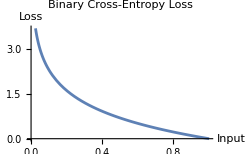

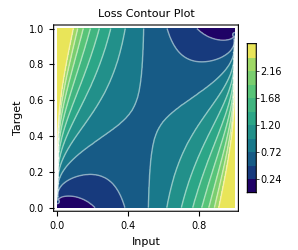

```mathematica
binaryCrossEntropyLoss[inputValue_,targetValue_]:=-(targetValue*Log[inputValue]+(1-targetValue)*Log[1-inputValue]);

lossValue=binaryCrossEntropyLoss[0.2,1]
builitInLoss=CrossEntropyLossLayer["Binary"][<|"Input"->0.2,"Target"->1|>]

Plot[
binaryCrossEntropyLoss[input,1],
{input,0,1},
ImageSize->250,
PlotLabel->"Binary Cross-Entropy Loss",
AxesLabel->{"Input","Loss"}
]

ContourPlot[
binaryCrossEntropyLoss[inputValue,targetValue],
{inputValue,0,1},
{targetValue,0,1},
Contours->10,
PlotLegends->Automatic,
PlotRangePadding->0,
FrameLabel->{"Input","Target"},
ImageSize->250,
PlotLabel->"Loss Contour Plot",
ContourStyle->{White},
ClippingStyle->Automatic,
ColorFunction->"BlueGreenYellow"
]
```

code 4.58

```mathematica
loss=CrossEntropyLossLayer["Binary","Input"->"Real"]
loss[<|"Input"->0.2,"Target"->0.8|>]
loss[<|"Input"->{0.2,0.1,0.1},"Target"->{0.8,0.9,0.1}|>]
```

CrossEntropyLossLayer[…]

1.33218

{1.33218,2.08286,0.325083}

### NetTrain

While we may not have yet completed the exhaustive theoretical groundwork necessary for training NNs, such as exploring various optimization methods and regularization techniques, it is imperative to take our first steps in practical application. In the realm of machine learning, theory and practice are intertwined, each informing and enriching the other.

Building a NN using off-the-shelf software can be likened to a child constructing a toy from building blocks. In both cases, you have distinct elements (blocks in the toy analogy, components or modules in the NN) that serve specific purposes. These components might include layers (such as linear layers, activation layers, etc.), optimizers, loss functions, and more in the context of NNs. Like assembling blocks, the process involves compatibility, a structured assembly process, trial and error, iteration, and opportunities for learning and creativity. Just as a child learns spatial reasoning and problem-solving skills through building with blocks, developers learn about NN architectures and optimization techniques through experimentation and refinement, aiming to achieve optimal performance with their models.

Let us begin training our networks using NetTrain in Mathematica. This process will be executed step by step. Initially, in this section, we provide a basic introduction, based on the theoretical foundations established in previous chapters to ensure a solid understanding. Subsequently, we will delve into more intricate details in the forthcoming chapters.

In this section, we will explore the diverse functionalities of the NetTrain function, understanding its syntax, parameters, and various forms.

NetTrain[net,{input1->output1,input2->output2,…}]	trains the specified neural net by giving the inputi as input and minimizing the discrepancy between the outputi and the actual output of the net, using an automatically chosen loss function.

NetTrain[net,<|port1->{data11,data12,…},port2->{…},…|>]	trains the specified net by supplying training data at the specified ports.

NetTrain[net,”dataset”]		trains on a named dataset from the Wolfram Data Repository.

NetTrain[net,f]			calls the function f during training to produce batches of training data.

NetTrain[net,data,”prop”]	gives data associated with a specific property prop of the training session.

NetTrain[net,data,All]		gives a NetTrainResultsObject[…] that summarizes information about the training session.

The following options are supported:

BatchSize		Automatic	how many examples to process in a batch

LearningRate		Automatic	rate at which to adjust weights to minimize loss

LearningRateMultipliers	Automatic	set relative learning rates within the net

LossFunction		Automatic	the loss function for assessing outputs

MaxTrainingRounds	Automatic	how many times to traverse the training data

Method			Automatic	the training method to use

PerformanceGoal	Automatic	favor settings with specific advantages

TargetDevice		“CPU”		the target device on which to perform training

TimeGoal		Automatic	number of seconds to train for

TrainingProgressMeasurements	Automatic	measurements to monitor, track and plot during training

TrainingProgressCheckpointing		None		how to periodically save partially trained nets

RandomSeeding		1234		how to seed pseudorandom generators internally

TrainingProgressFunction	None		function to call periodically during training

TrainingProgressReporting	Automatic	how to report progress during training

TrainingStoppingCriterion	None		how to automatically stop training

TrainingUpdateSchedule	Automatic	when to update specific parts of the net

ValidationSet			None		the set of data on which to evaluate the model during training

WorkingPrecision		Automatic	precision of floating-point calculations

Remarks:

• Any input ports of the net whose shapes are not fixed will be inferred from the form of training data.

• Individual training data inputs can be scalars, vectors, numeric tensors.

• If the loss is not given explicitly using LossFunction, a loss function will be chosen automatically based on the final layer or layers in the net.

• With the default setting of BatchSize->Automatic, the batch size will be chosen automatically, based on the memory requirements of the network and the memory available on the target device. The maximum batch size that will be automatically chosen is 64.

• With the default setting of MaxTrainingRounds->Automatic, training will occur for approximately 20 seconds, but never for more than 10,000 rounds.

• With the setting of MaxTrainingRounds->n, training will occur for n rounds, where a round is defined to be a traversal of the entire training dataset.

• NetTrain[net,data,All] returns a NetTrainResultsObject[…] that contains values for all properties that do not require significant additional computation or memory.

• NetTrainResultsObject[…][prop] is used to look up property prop from the NetTrainResultsObject.

• Properties supported include: “ArraysLearningRateMultipliers”, “BatchesPerRound”, “BatchLossList”, “BatchMeasurementsLists”, “BatchSize”, “BestValidationRound”, “CheckpointingFiles”, “ExamplesProcessed”, “FinalLearningRate”, “FinalPlots”, “InitialLearningRate”, “LossPlot”, “MeanBatchesPerSecond”, “MeanExamplesPerSecond”, “NetTrainInputForm”, “OptimizationMethod”, “ReasonTrainingStopped”, “RoundLoss”, “RoundLossList”, “RoundMeasurements”, “RoundMeasurementsLists”, “RoundPositions”, “TargetDevice”, “TotalBatches”, “TotalRounds”, “TotalTrainingTime”, “TrainedNet”, “TrainingExamples”, “TrainingNet”, “ValidationExamples”, “ValidationLoss”, “ValidationLossList”, “ValidationMeasurements”, “ValidationMeasurementsLists”, and “ValidationPositions”

• If a net already contains initialized or previously trained weights, these will be not be reinitialized by NetTrain before training is performed.

Possible settings for Method include:

“ADAM”		stochastic gradient descent using an adaptive learning rate that is invariant to diagonal rescaling of the gradients

“RMSProp”	stochastic gradient descent using an adaptive learning rate derived from exponentially smoothed average of gradient magnitude

“SGD”		ordinary stochastic gradient descent with momentum

“SignSGD” 	stochastic gradient descent for which the magnitude of the gradient is discarded

Suboptions for specific methods can be specified using Method->{“method”,opt1->val1,…}. The following suboptions are supported for all methods:

“LearningRateSchedule”Automatic 	how to scale the learning rate as training progresses

“L2Regularization” 	None		the global loss associated with the L2 norm of all learned arrays

“GradientClipping”	None		the magnitude above which gradients should be clipped

“WeightClipping”	None 		the magnitude above which weights should be clipped

code 4.59

(* The code demonstrates the basics of training a linear neural network for a simple regression task and visualizing the learned function: *)

LinearLayer[…]

6.305

{2.95,6.,9.05,12.1}

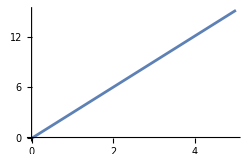

{6.,9.05,12.1,15.15}

```mathematica
trainednet=NetTrain[
LinearLayer[],
{1->2.9,2->6.1,3->9.0,4->12.1},
BatchSize->4,
MaxTrainingRounds->500,
LearningRate->0.01,
LossFunction->MeanSquaredLossLayer[],
Method->"SGD"
]

trainednet[2.1]
trainednet[{1,2,3,4}]

Plot[trainednet[x],
{x,0,5},
ImageSize->250
]

trainednet[{2,3,4,5}]
```

code 4.60

(* This code creates and trains a neural network (NetChain) with a specific architecture {1,3,3,1}. It then uses input-output pairs for training, specified in a similar manner as the previous example: *)

```mathematica
trainedNetwork=NetTrain[
NetChain[{1,3,3,1}],
{1->2.9,2->6.1,3->9.0,4->12.1},
BatchSize->4,
MaxTrainingRounds->500,
LearningRate->0.001,
LossFunction->MeanSquaredLossLayer["Target"->"Scalar"],
Method->"SGD"
]

multiplePredictions=trainedNetwork[{2,3,4,5}]
```

NetChain[…]

{5.99999,9.05,12.1,15.15}

code 4.61

(* Neural Network Training with Directed Graph: *) (* This code creates and trains a neural network (NetGraph) with a directed graph of layers {1,3,3,1}. The connections between layers are specified by the graph {1->2->3->4}. Training data, as input-output pairs, is provided in a similar manner as the previous examples: *)

```mathematica
directedGraphNet=NetTrain[
NetGraph[{1,3,3,1},{1->2->3->4}],
{1->2.9,2->6.1,3->9.0,4->12.1},
BatchSize->4,
MaxTrainingRounds->500,
LearningRate->0.001,
LossFunction->MeanSquaredLossLayer["Target"->"Scalar"],
Method->"SGD"
]

multiplePredictions=directedGraphNet[{2,3,4,5}]
```

NetGraph[…]

{5.99999,9.05,12.1,15.15}

code 4.62

(* Neural Network Training and Data Representation: *) (* Note that: If you don’t explicitly specify hyperparameters such as learning rate, batch size, etc., Mathematica will use default values for these parameters during the training process. Defaults are pre-set values chosen by the developers of the neural network functions in Mathematica. These defaults are often chosen to work well across a broad range of problems, but they may not be optimal for every specific case. If you have a specific problem or dataset, it’s often a good practice to experiment with different hyperparameter values to find the combination that works best for your particular scenario: *) (* The following comments explain how the training data is represented in different formats, including rules, lists, and associations: *)

```mathematica
NetTrain[
LinearLayer[],
{1->2.9,2->6.1,3->9.0,4->12.1},
MaxTrainingRounds->500
]

NetTrain[
LinearLayer[],
{1,2,3,4}->{2.9,6.1,9.,12.1},
MaxTrainingRounds->500
]

NetTrain[
LinearLayer[],
<|"Input"->{1,2,3,4},"Output"->{2.9,6.1,9.,12.1}|>,
MaxTrainingRounds->500
]

NetTrain[LinearLayer[],{
<|"Input"->1,"Output"->2.9|>,
<|"Input"->2,"Output"->6.1|>,
<|"Input"->3,"Output"->9.|>,
<|"Input"->4,"Output"->12.1|>},
MaxTrainingRounds->500
]
```

LinearLayer[…]

LinearLayer[…]

LinearLayer[…]

«1 more identical outputs»

code 4.63

(* Regression with Noisy Sine Wave Dataset: *) (* This example creates a simple feedforward neural network, trains it on a noisy sine wave dataset, and then tests it on a new input. The network architecture consists of three hidden layers with 25, 5, and 1 neurons, respectively. Tanh activation functions are applied after the linear layers to introduce non-linearity: *)

NetChain[…]

NetChain[…]

-Graphics-

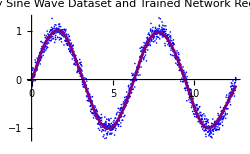

```mathematica
SeedRandom[123];

inputs=Table[x,{x,0,4 π,0.01}];
target=Table[
Sin[x]+RandomVariate[NormalDistribution[0,0.1]],
{x,0,4π,0.01}
];

data=Transpose[{inputs,target}];

regressionNetwork=NetChain[
{
LinearLayer[25],ElementwiseLayer[Tanh],
LinearLayer[5],ElementwiseLayer[Tanh],
LinearLayer[1]}
]

trainedNetwork=NetTrain[
regressionNetwork,
<|"Input"->inputs,"Output"->target|>,
MaxTrainingRounds->1000
]

Information[trainedNetwork,"SummaryGraphic"]

Show[
ListPlot[
data,
PlotStyle->Blue,
ImageSize->250,
PlotLabel->"Noisy Sine Wave Dataset and Trained Network Regression"
],
Plot[
trainedNetwork[x],
{x,0,4π},
PlotStyle->Purple,
ImageSize->250]
]
```

code 4.64

(* Regression with Neural Network: *) (* The code aims to illustrate the training of a neural network for a regression task on a 2D dataset, visualize the learned function, and evaluate the network’s prediction on a specific input: *)

```mathematica
trainingData=Flatten@Table[
{x,y}->Exp[-Norm[{x,y}]],
{x,-3,3,.005},
{y,-3,3,.005}
];

regressionNetwork=NetChain[{32,Tanh,1}];

trainedNetwork=NetTrain[
regressionNetwork,
trainingData,
BatchSize->1024,
MaxTrainingRounds->10,
LearningRate->0.01,
LossFunction->MeanSquaredLossLayer["Target"->"Scalar"],
Method->"SGD"
];

prediction=trainedNetwork[{1,0}]

Plot3D[
trainedNetwork[{x,y}],
{x,-2,2},
{y,-2,2},
ImageSize->250,
ColorFunction->"Rainbow",
PlotLegends->Automatic,
NormalsFunction->None,
PlotLabel->"3D Plot of Predicted Output"
]
```

0.385327

-Graphics3D-

code 4.65

(* Neural Network Training and Performance Visualization: *) (* The code demonstrates how a neural network can be trained on noisy data to learn the underlying patterns, and how the trained network can be used to make predictions on new input data. The visualizations help in assessing the performance of the trained network and comparing it to the noisy dataset: *)

NetChain[…]

NetChain[…]

-Graphics3D-

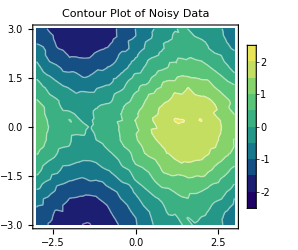

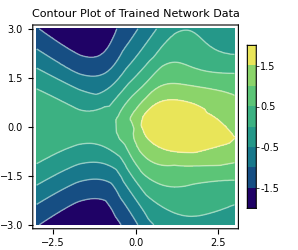

```mathematica
SeedRandom[123];

noisyData=Flatten[
Table[
{{x,y,Sin[x]+Cos[y]+RandomVariate[NormalDistribution[0,0.05]]}},
{x,-3,3,0.2},
{y,-3,3,0.2}
],
2
];

trainingData=Flatten[
Table[
{{x,y}->Sin[x]+Cos[y]+RandomVariate[NormalDistribution[0,0.05]]},
{x,-3,3,0.2},
{y,-3,3,0.2}],
2
];

regressionNetwork=NetChain[
{
LinearLayer[15],ElementwiseLayer[Ramp],
LinearLayer[15],ElementwiseLayer[Tanh],
LinearLayer[1]
}
]

trainedNetwork=NetTrain[
regressionNetwork,
trainingData,
MaxTrainingRounds->50
]

ListPointPlot3D[
noisyData,
ColorFunction->"Rainbow",
PlotLegends->Automatic,
ImageSize->250,
PlotLabel->"3D Point Plot of Noisy Data"
]

ListContourPlot[
noisyData,
ContourStyle->{White},
ClippingStyle->Automatic,
ColorFunction->"BlueGreenYellow",
PlotLegends->Automatic,
LabelStyle->Directive[Black,10],
PlotLabel->"Contour Plot of Noisy Data",
ImageSize->250
]

ContourPlot[
trainedNetwork[{x,y}],
{x,-3,3},
{y,-3,3},
ContourStyle->{White},
ClippingStyle->Automatic,
ColorFunction->"BlueGreenYellow",
PlotLegends->Automatic,
LabelStyle->Directive[Black,10],
ImageSize->250,
PlotLabel->"Contour Plot of Trained Network Data"
]
```

code 4.66

(* Neural Network Training and Analysis: *) (* The code demonstrates how to use the NetTrainResultsObject to query and access various training-related information after training a neural network: *)

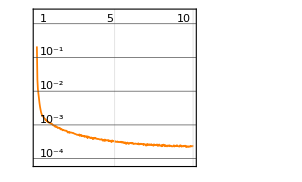
NetTrainResultsObject[NetTrain Results
summary | ,,  batches:14090  rounds:10  time:19s  examples/s:773207
data | ,,  training examples:1442401  processed examples:14428160  skipped examples:0
method | ,,  SGDoptimizer  batch size1024CPU
round | ,,  loss:2.33×10^-4
 | rounds
loss | -Graphics- | 
 | ]

1409

1024

| rounds
loss | -Graphics-

{SGD,GradientClipping→None,L2Regularization→None,LearningRate→0.01,LearningRateSchedule→Polynomial,Momentum→0.93,WeightClipping→None}

0.01

18.6602

NetChain[…]

NetGraph[…]

{ArraysLearningRateMultipliers,BatchesPerRound,BatchesPerSecond,BatchLossList,BatchMeasurements,BatchMeasurementsLists,BatchSize,BestValidationRound,CheckpointingFiles,ExamplesProcessed,FinalLearningRate,FinalPlots,InitialLearningRate,InternalVersionNumber,LossPlot,MeanBatchesPerSecond,MeanExamplesPerSecond,NetTrainInputForm,OptimizationMethod,ReasonTrainingStopped,RoundLoss,RoundLossList,RoundMeasurements,RoundMeasurementsLists,RoundPositions,SkippedTrainingData,TargetDevice,TotalBatches,TotalRounds,TotalTrainingTime,TrainedNet,TrainingExamples,TrainingNet,TrainingUpdateSchedule,ValidationExamples,ValidationLoss,ValidationLossList,ValidationMeasurements,ValidationMeasurementsLists,ValidationPositions}

```mathematica
data=Flatten@Table[
{x,y}->Exp[-Norm[{x,y}]],
{x,-3,3,0.005},
{y,-3,3,0.005}
];

regressionNetwork=NetChain[{32,Tanh,1}];

trainingResults=NetTrain[
regressionNetwork,
data,
All,
BatchSize->1024,
MaxTrainingRounds->10,
LearningRate->0.01,
LossFunction->MeanSquaredLossLayer["Target"->"Scalar"],
Method->"SGD"
]

batchesPerRound=trainingResults["BatchesPerRound"]
batchSize=trainingResults["BatchSize"]
lossPlot=trainingResults["LossPlot"]
optimizationMethod=trainingResults["OptimizationMethod"]
initialLearningRate=trainingResults["InitialLearningRate"]
totalTraingingTime=trainingResults["TotalTrainingTime"]
trainedNet=trainingResults["TrainedNet"]
trainingNet=trainingResults["TrainingNet"]

allProperties=trainingResults["Properties"]
```

code 4.67

(* The code demonstrates the training and usage of a simple perceptron for binary classification and visualize its behavior in terms of probability across a range of inputs: *)

NetChain[…]

True

0.974409

{False,False,False,False,True,True,True,True}

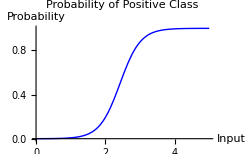

```mathematica
classificationPerceptron=NetChain[{LinearLayer[],LogisticSigmoid}];

trainedPerceptron=NetTrain[
classificationPerceptron,
{1->False,2->False,3->True,4->True}
]

predictionSingleInput=trainedPerceptron[3.5]

probabilitySingleInput=trainedPerceptron[3.5,None]

predictionsMultipleInputs=trainedPerceptron[{-1,0,1,2,3,4,5,6}]

Plot[
trainedPerceptron[x,None],
{x,0,5},
ImageSize->250,
PlotLabel->"Probability of Positive Class",
AxesLabel->{"Input","Probability"},
PlotStyle->Directive[Blue,Thick]
]
```

code 4.68

(* The code serves to illustrate the impact of nonlinearity in classification networks, emphasizing the importance of incorporating nonlinear activation functions to handle complex relationships in data, especially in scenarios where classes are not linearly separable. Create a synthetic training set consisting of points on a disk, separated into two classes by the circle r=0.5: *)

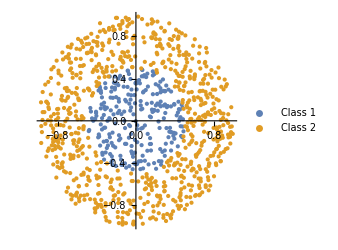

NetChain[…]

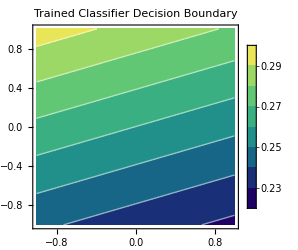

```mathematica
points=RandomPoint[Disk[],1000];
labels=Thread[Map[Norm,points]<0.5];

trainingData=points->labels;

ListPlot[
{Pick[points,labels,True],Pick[points,labels,False]},
AspectRatio->1,
ImageSize->250,
PlotStyle->PointSize[Medium],
FrameLabel->{"X","Y","Synthetic Training Set"},PlotLegends->{"Class 1","Class 2"}
]

classificationNet=NetChain[
{LinearLayer[20],LinearLayer[],ElementwiseLayer[LogisticSigmoid]},
"Output"->NetDecoder["Boolean"]
]

trainedClassifier=NetTrain[classificationNet,trainingData];

ContourPlot[
trainedClassifier[{x,y},None],
{x,-1,1},
{y,-1,1},
ContourStyle->{White},
ClippingStyle->Automatic,
ColorFunction->"BlueGreenYellow",
PlotLegends->Automatic,
LabelStyle->Directive[Black,10],
ImageSize->250,
PlotLabel->"Trained Classifier Decision Boundary"
]
```

(* Because LinearLayer is an affine layer, stacking the two layers without an intervening nonlinearity is equivalent to using a single layer. A single line in the plane cannot separate the two classes, which is the level set of a single LinearLayer: *)

NetChain[…]

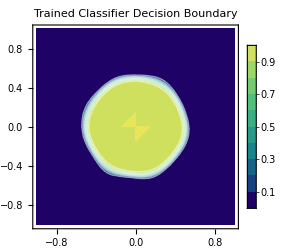

```mathematica
nonlinearClassifier=NetChain[
{
LinearLayer[20],ElementwiseLayer[Tanh],
LinearLayer[],ElementwiseLayer[LogisticSigmoid]
},
"Output"->NetDecoder["Boolean"]
]

trainedNonlinearClassifier=NetTrain[nonlinearClassifier,trainingData];

ContourPlot[
trainedNonlinearClassifier[{x,y},None],
{x,-1,1},
{y,-1,1},
ContourStyle->{White},
ClippingStyle->Automatic,
ColorFunction->"BlueGreenYellow",
PlotLegends->Automatic,
LabelStyle->Directive[Black,10],
ImageSize->250,
PlotLabel->"Trained Classifier Decision Boundary"
]
```